# Definitions

## Defining different parameters, ALP models and their RG flow, ChPT

```mathematica
DirectoryRoutines=FileNameJoin[{NotebookDirectory[],"notebooks"}];
Print["Defining ALP models..."]
Block[{Print=Identity},
(*Parameters and functions*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"dialog-windows.nb"}]];
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-models.nb"}]];
];//AbsoluteTiming
Print["Defining baseline parameters and functions..."]
Block[{Print=Identity},
(*Parameters and functions*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"parameters-functions.nb"}]];
];//AbsoluteTiming
Print["Launching routines to compute/load running of the ALP couplings..."]
Block[{Print=Identity},
(*Running of ALP couplings*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-running.nb"}]];
];//AbsoluteTiming
Print["Choice of the η-η' mixing angle:"]
θηηPrChoice= θηStandard
Print["Launching the notebook defining ChPT Lagrangian..."]
Block[{Print=Identity},
(*ChPT in SM*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"chpt-SM.nb"}]];
]//AbsoluteTiming
```

Defining ALP models...

{0.205936,Null}

Defining baseline parameters and functions...

Identity::argx: Identity called with 9 arguments; 1 argument is expected.

{4.27248,Null}

Launching routines to compute/load running of the ALP couplings...

{2.12157,Null}

Choice of the η-η' mixing angle:

-sin^-1(1/3)

Launching the notebook defining ChPT Lagrangian...

{11.4578,Null}

## Defining ALP-meson mixing

## Setup

```mathematica
(*Whether use κ-independent approach a-la https://arxiv.org/abs/2501.04525 or κ-variant approach from https://arxiv.org/abs/1811.03474*)
Print["If using κ-invariant description of the phenomenology:"]
IfκInv=(*True*)True
Print["If including mixing with heavy pseudoscalar excitations:"]
IfPheavy=(*True*)True
```

If using κ-invariant description of the phenomenology:

True

If including mixing with heavy pseudoscalar excitations:

True

## Sector of light mesons π^0,η,η'

```mathematica
Print["Launching the notebook diagonalizing the quadratic Lagrangian with ALPs and lightest pseudoscalar mesons, and defining mixing angles..."]
Block[{Print=Identity},
(*ChPT with ALPs*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-diagonalization.nb"}]];
]//AbsoluteTiming
Print["Mass and kinetic mixing matrices between ALPs and mesons π^0, η, η':"]
Join[{{""},{"a"},{"π^0"},{"η"},{"η'"}},Join[{{"a","π^0","η","η'"}},Table[Mm0X[particle1,particle2],{particle1,listMesonP0a},{particle2,listMesonP0a}]],2]
Join[{{""},{"a"},{"π^0"},{"η"},{"η'"}},Join[{{"a","π^0","η","η'"}},Table[Km0X[particle1,particle2],{particle1,listMesonP0a},{particle2,listMesonP0a}]],2]
Print["ALP-meson mixing descriptions:"]
{#,mixingDescriptionMeaning[#]}&/@mixingDescriptionKeys
tabMixingAngles[description_,CU_,CD_,CS_,CG_]:={{"Meson","π^0","η","η'"},{"θ_(am^0)",θm0ALP["π^0",description],θm0ALP["η",description],θm0ALP["η'",description]}}/.{cu->CU,cd->CD,cs->CS,cG->CG}
Print["Selected mixing description:"]
choiceMixingDescription=selectionDialogExplanationOneOption[mixingDescriptionKeys,mixingDescriptionMeaning[#]&/@mixingDescriptionKeys,"Select the description of the ALP-meson mixing",100]
tabMixingAngles[choiceMixingDescription,cu,cd,cs,cG]
```

Launching the notebook diagonalizing the quadratic Lagrangian with ALPs and lightest pseudoscalar mesons, and defining mixing angles...

{34.27,Null}

Mass and kinetic mixing matrices between ALPs and mesons π^0, η, η':

( | a | π^0 | η | η'
a | ma^2 | -cG mπ0^2 ϵ ((δ+1) κd+(δ-1) κu) | √(2/3) cG ϵ (2 mη^2 (κd+κu-1)+mπ0^2 (δ (κd-κu)+1)) | (cG ϵ (mπ0^2 ((δ+3) κd-δ κu+3 κu-2)-4 mη^2 (κd+κu-1)))/(√3)
π^0 | -cG mπ0^2 ϵ ((δ+1) κd+(δ-1) κu) | mπ0^2 | -√(2/3) δ mπ0^2 | -(δ mπ0^2)/(√3)
η | √(2/3) cG ϵ (2 mη^2 (κd+κu-1)+mπ0^2 (δ (κd-κu)+1)) | -√(2/3) δ mπ0^2 | mη^2 | 0
η' | (cG ϵ (mπ0^2 ((δ+3) κd-δ κu+3 κu-2)-4 mη^2 (κd+κu-1)))/(√3) | -(δ mπ0^2)/(√3) | 0 | mηpr^2)

( | a | π^0 | η | η'
a | 1 | ϵ (-cd+cG (κu-κd)+cu) | √(2/3) ϵ (cd+cG (2 κd+2 κu-1)-cs+cu) | (ϵ (cd-cG (κd+κu-2)+2 cs+cu))/(√3)
π^0 | ϵ (-cd+cG (κu-κd)+cu) | 1 | 0 | 0
η | √(2/3) ϵ (cd+cG (2 κd+2 κu-1)-cs+cu) | 0 | 1 | 0
η' | (ϵ (cd-cG (κd+κu-2)+2 cs+cu))/(√3) | 0 | 0 | 1)

ALP-meson mixing descriptions:

(O(δ,ϵ) | Baseline description
No π^0-η/η' mixing | Dropping the terms coming from the mass mixing of π^0 with η/η' mesons in the expressions for the mixing angles θ_(am^0). This approximation is used in 1811.03474. It is similar to dropping O(δ×(m^2)_π/(m^2)_η) terms
Only π^0a | π^0-ALP mixing only)

Selected mixing description:

O(δ,ϵ)

(Meson | π^0 | η | η'
θ_(am^0) | (-(2 δ mπ0^2 ϵ (ma^2 (cs-cu)-cd ma^2))/(3 (ma^2-mη^2))+(δ mπ0^2 ϵ (cd ma^2+ma^2 (2 cs+cu)))/(3 (ma^2-mηpr^2))-(ma^2 ϵ (cu-cd)))/(ma^2-mπ0^2)+(cG ((δ mπ0^2 ϵ (2 ma^2-mηpr^2-mπ0^2))/(3 (ma^2-mηpr^2))-(2 δ mπ0^2 ϵ (ma^2-2 mη^2+mπ0^2))/(3 (ma^2-mη^2))))/(ma^2-mπ0^2)+cG ϵ (κd-κu) | (-√(2/3) ma^2 ϵ (cd-cs+cu)-(√(2/3) δ ma^2 mπ0^2 ϵ (cd-cu))/(ma^2-mπ0^2))/(ma^2-mη^2)+(cG (√(2/3) ma^2 ϵ+√(2/3) ϵ (mπ0^2-2 mη^2)))/(ma^2-mη^2)-2 √(2/3) cG ϵ (κd+κu) | (-(ϵ (cd ma^2+ma^2 (2 cs+cu)))/(√3)-(δ ma^2 mπ0^2 ϵ (cd-cu))/(√3 (ma^2-mπ0^2)))/(ma^2-mηpr^2)-(cG ϵ (2 ma^2-mηpr^2-mπ0^2))/(√3 (ma^2-mηpr^2))+(cG ϵ (κd+κu))/(√3))

## Sector of heavy mesons π^0(1300),η(1295),η(1440). Using LSM approach from https://arxiv.org/pdf/1612.09218

```mathematica
Print["Launching the notebook diagonalizing the quadratic Lagrangian with ALPs and heavier pseudoscalar mesons, and defining mixing angles..."]
Block[{Print=Identity},
(*ChPT with ALPs*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-diagonalization-heavy.nb"}]];
]//AbsoluteTiming
Print["Mass and kinetic mixing matrices between ALPs and mesons π^0(1300), η(1295), η(1440):"]
Join[{{""},{"a"},{"π^0(1300)"},{"η(1295)"},{"η(1440)"}},Join[{{"a","π^0(1300)","η(1295)","η(1440)"}},Table[Mm0heavyX[particle1,particle2],{particle1,listMesonP0heavya},{particle2,listMesonP0heavya}]],2]
Join[{{""},{"a"},{"π^0(1300)"},{"η(1295)"},{"η(1440)"}},Join[{{"a","π^0(1300)","η(1295)","η(1440)"}},Table[Km0heavyX[particle1,particle2],{particle1,listMesonP0heavya},{particle2,listMesonP0heavya}]],2]
{{"Meson","π^0(1300)","η(1295)","η(1440)"},{"θ_(am^0)",θm0heavyALP["π^0(1300)"],θm0heavyALP["η(1295)"],θm0heavyALP["η(1440)"]}}
ruleSymbolsToNumbersFinal[expr_,δorder_]:=ruleSymbolsToNumbers[expr,choiceMixingDescription,δorder]
```

Launching the notebook diagonalizing the quadratic Lagrangian with ALPs and heavier pseudoscalar mesons, and defining mixing angles...

{2.74898,Null}

Mass and kinetic mixing matrices between ALPs and mesons π^0(1300), η(1295), η(1440):

( | a | π^0(1300) | η(1295) | η(1440)
a | ma^2 | -1/2 cG ϵ (κd-κu) (ϕN^2 (λ2star-ξ2)+2 m0star^2) | 1/2 cG ϵ (κd+κu) (ϕN^2 (λ2star-ξ2)+2 m0star^2) | -√2 cG ϵ (κd+κu-1) (ϕS^2 (λ2star-ξ2)+m0star^2-2 ϵS)
π^0(1300) | -1/2 cG ϵ (κd-κu) (ϕN^2 (λ2star-ξ2)+2 m0star^2) | mπ01300^2 | 0 | 0
η(1295) | 1/2 cG ϵ (κd+κu) (ϕN^2 (λ2star-ξ2)+2 m0star^2) | 0 | mη1295^2 | 0
η(1440) | -√2 cG ϵ (κd+κu-1) (ϕS^2 (λ2star-ξ2)+m0star^2-2 ϵS) | 0 | 0 | mη1440^2)

( | a | π^0(1300) | η(1295) | η(1440)
a | 1 | ϵ (-cd+cG (κu-κd)+cu) | ϵ (cd+cG (κd+κu)+cu) | √2 ϵ (cs-cG (κd+κu-1))
π^0(1300) | ϵ (-cd+cG (κu-κd)+cu) | 1 | 0 | 0
η(1295) | ϵ (cd+cG (κd+κu)+cu) | 0 | 1 | 0
η(1440) | √2 ϵ (cs-cG (κd+κu-1)) | 0 | 0 | 1)

(Meson | π^0(1300) | η(1295) | η(1440)
θ_(am^0) | cG ϵ (κd-κu)-(ma^2 ϵ (cu-cd))/(ma^2-mπ01300^2) | -(ma^2 ϵ (cd+cu))/(ma^2-mη1295^2)-cG ϵ (κd+κu) | √2 cG ϵ (κd+κu)-√2 cG ϵ-(√2 cs ma^2 ϵ)/(ma^2-mη1440^2))

## Defining ALP interactions with mesons

```mathematica
Print["Generating the κ-invariant Lagrangian of the interaction of the ALPs with different mesons..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-SVT.nb"}]];
];//AbsoluteTiming
Print["Defining the kinematics of n-body decays..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"n-body-decays.nb"}]];
];//AbsoluteTiming
Print["Defining Feynman rules for various vertices..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"feynman-rules.nb"}]];
];//AbsoluteTiming
```

Generating the κ-invariant Lagrangian of the interaction of the ALPs with different mesons...

\frac{\sqrt{2} \alpha  \epsilon  \left(m_a^2-m_{\pi }^2\right) \text{alp}(x) c_G \text{$\eta $1440}(x) \left(m_{\eta }^2-m_{\eta '}^2\right)}{3 \left(m_a^2-m_{\eta }^2\right) \left(m_a^2-m_{\eta '}^2\right)}-\frac{\alpha  \epsilon  \text{alp}(x)
   c_G \text{$\eta $1295}(x) \left(m_a^2 \left(m_{\eta '}^2+2 m_{\eta }^2-3 m_{\pi }^2\right)+2 m_{\pi }^2 m_{\eta '}^2+m_{\eta }^2 \left(m_{\pi }^2-3 m_{\eta '}^2\right)\right)}{3 \left(m_a^2-m_{\eta }^2\right) \left(m_a^2-m_{\eta '}^2\right)}

{10.1285,Null}

Defining the kinematics of n-body decays...

{2.01396,Null}

Defining Feynman rules for various vertices...

{0.559156,Null}

## Some information about the input and output

## List of ALP models and their illustrative RG flow

```mathematica
Print["Coupling pattern (defined at some scale Λ):"]
Join[{Join[{"Model"},ALPcouplingslist]},Join[Partition[ModelListAll,1],Table[couplingPatternOverall[model],{model,ModelListAll}],2]]//TableForm
Λillustration=10^3.;
Print[Row[{"RG flow to low scales μ ~ 1 GeV assuming Λ = ",10^-3. Λillustration," TeV:"}]]
Join[{Join[{"Model"},ALPcouplingslist]},Join[Partition[ModelListAll,1],Table[cRGval[model,Λillustration,#]&/@ALPcouplingslist,{model,ModelListAll}],2]]//TableForm
```

Coupling pattern (defined at some scale Λ):

Model | cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
B | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
Fermion universal | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0
Gluon | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
Gluon 1811.03474 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
Quark universal | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
W | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0

RG flow to low scales μ ~ 1 GeV assuming Λ = 1. TeV:

Model | cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
B | 0. | 0. | 0. | 0. | 0. | -8.692×10^-6 | 0. | 0. | 0. | 0. | 0. | 1.
Fermion universal | 0.873891 | 0.986109 | 0.986109 | 0.873891 | 1.04676 | 0.906242 | 0. | 1.05611 | 1.05611 | 1.05611 | 0. | 0.
Gluon | -0.0166131 | -0.0166131 | -0.0166131 | -0.0166131 | -0.00161308 | -0.00153926 | 1. | 0. | 0. | 0. | 0. | 0.
Gluon 1811.03474 | -0.00830654 | -0.00830654 | -0.00830654 | -0.00830654 | -0.000806538 | -0.000769639 | 0.5 | 0. | 0. | 0. | 0. | 0.
Quark universal | 0.873891 | 0.986109 | 0.986109 | 0.873891 | 1.04676 | 0.906357 | 0. | 0.0561092 | 0.0561092 | 0.0561092 | 0. | 0.
W | 0. | 0. | 0. | 0. | 0. | -0.0000505385 | 0. | 0. | 0. | 0. | 1. | 0.

## Mixing angles plot

### With light pseudoscalars

ALP-meson mixing angles (here, assuming the standard replacement for the κ matrix κ = (m^-1)_q/Tr[(m^-1)_q]:

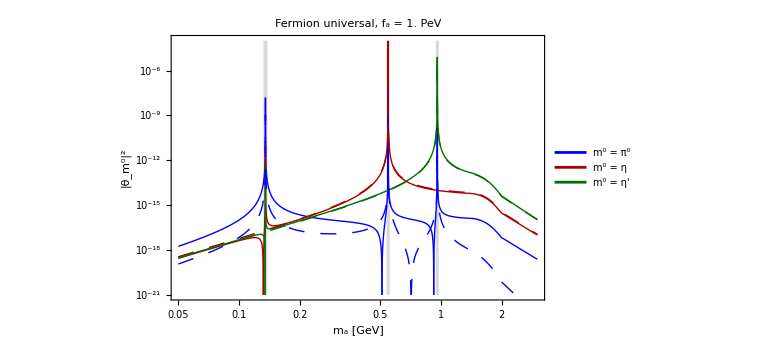
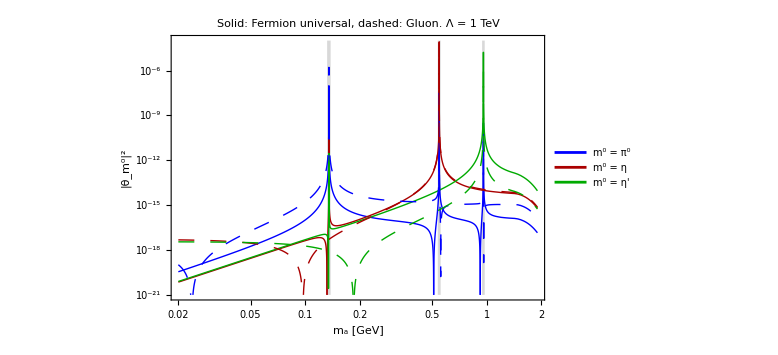

```mathematica
Print["ALP-meson mixing angles (here, assuming the standard replacement for the κ matrix κ = (m^-1)_q/Tr[(m^-1)_q]:"]
(*Numeric expressions for the mixing angles - multiplied with the ChPT suppression*)
Do[
(*θm0a[model,Λ_,meson,ma_,fa_]=Ffunction[ma]*ruleSymbolsToNumbersFinal[θm0ALP[meson,choiceMixingDescription]/.replacementκ,2]/.Evaluate[tableValuesReplacement[model,Λ]];*)
θm0a[model,Λ_,meson,ma_,fa_]=Ffunction[ma]*(ruleSymbolsToNumbersFlexible[θm0ALP[meson,choiceMixingDescription]/.{cG->0},choiceMixingDescription,1,False,True]+cG*ruleSymbolsToNumbersFlexible[D[θm0ALP[meson,choiceMixingDescription],cG],choiceMixingDescription,1,False,True])/.Evaluate[tableValuesReplacement[model,Λ]];
θ2m0a[model,Λ_,meson,ma_,fa_]=Abs[θm0a[model,Λ,meson,ma,fa]]^2;
,{meson,listMesonP0},{model,ModelListAll}]
fval=10^6;
Λval=10^3;
plotmixingangles[model_]:=LogLogPlot[Evaluate[Join[θ2m0a[model,Λval,#,ma,fval]&/@listMesonP0,θ2m0a[model,MASS["t"],#,ma,fval]&/@listMesonP0,{10^30 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^30 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^10 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)]}]],{ma,0.05,3},PlotPoints->500,PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue,Dashing[0.02]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black},{Thick,Darker@Green},{Thick,Darker@Green,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[Row[{"m^0 = " ,#}],22]&/@listMesonP0,{0.13,0.8}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "|θ_(m^0)|^2"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->{{0.05,3},{(10^3/fval)^2 10^-15,(10^3/fval)^2 100}},PlotLabel->Style[Row[{model, ", f_a = "<>ToString[10^-6. faval]<>" PeV"}],22,Black],Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}}]
modeltest="Fermion universal";
pt1=plotmixingangles[modeltest];
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Mixing-angles-``.pdf",Sequence@@{modeltest}]}],plotmixingangles[modeltest]];
mods={"Fermion universal","Gluon"};
pt2=LogLogPlot[Evaluate[Join[Flatten[Table[θ2m0a[#,Λval,mes,ma,fval],{mes,listMesonP0}]&/@mods],{10^30 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^30 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^10 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)]}]],{ma,0.02,1.9},PlotRange->{{0.02,1.9},{(10^3/fval)^2 10^-15,(10^3/fval)^2 100}},Frame->True,ImageSize->Large,PlotStyle->Evaluate[Join[({Thick,#}&/@{Blue,Darker@Red,Darker@Green}),({Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red,Darker@Green})]],PlotLegends->Placed[Style[Row[{"m^0 = ",#}],22,Black]&/@listMesonP0,{0.13,0.8}],FrameStyle->Directive[Thick,Black,22],PlotLabel->Style[Row[{"Solid: ",mods[[1]],", dashed: ",mods[[2]],". Λ = ",10^-3 Λval," TeV"}],18,Thick,Black],FrameLabel->{"m_a [GeV]","|θ_(m^0)|^2"},Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}},PlotPoints->500];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]
```

### With heavy pseudoscalars

ALP-meson mixing angles (here, assuming the standard replacement for the κ matrix κ = (m^-1)_q/Tr[(m^-1)_q]:

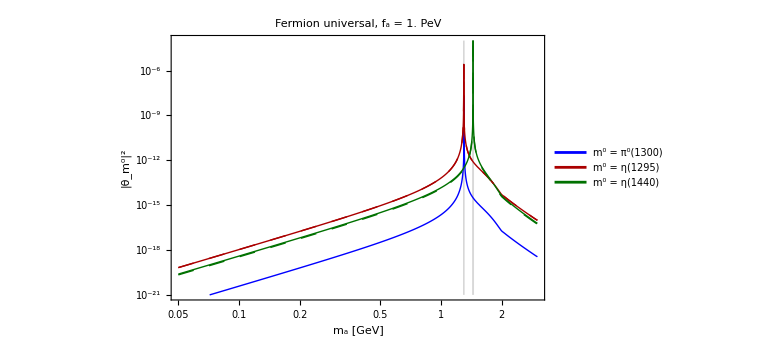
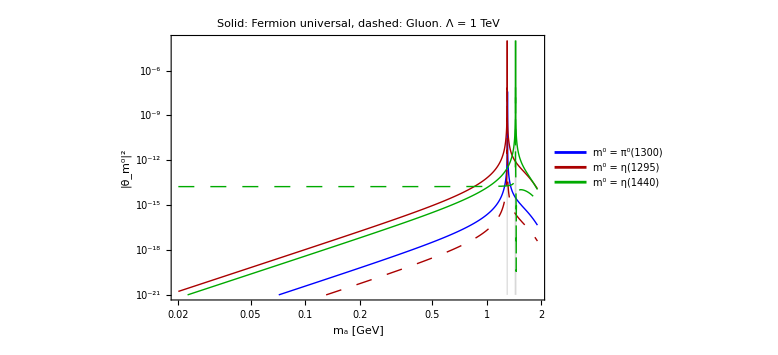

```mathematica
(*Numeric expressions for the mixing angles - multiplied with the ChPT suppression*)
Print["ALP-meson mixing angles (here, assuming the standard replacement for the κ matrix κ = (m^-1)_q/Tr[(m^-1)_q]:"]
Do[
θm0heavya[model,Λ_,meson,ma_,fa_]=Ffunction[ma]*ruleSymbolsToNumbersFinal[θm0heavyALP[meson]/.replacementκ,2]/.Evaluate[tableValuesReplacement[model,Λ]];
θ2m0heavya[model,Λ_,meson,ma_,fa_]=Abs[θm0heavya[model,Λ,meson,ma,fa]]^2;
,{meson,listMesonP0heavy},{model,ModelListAll}]
fval=10^6;
Λval=10^3;
plotmixingangles[model_]:=LogLogPlot[Evaluate[Join[θ2m0heavya[model,Λval,#,ma,fval]&/@listMesonP0heavy,θ2m0heavya[model,MASS["t"],#,ma,fval]&/@listMesonP0heavy,{10^30 UnitStep[(MASS["π^0(1300)"]+0.003)-ma]*UnitStep[ma-(MASS["π^0(1300)"]-0.003)],10^30 UnitStep[(MASS["η(1295)"]+0.01)-ma]*UnitStep[ma-(MASS["η(1295)"]-0.01)],10^10 UnitStep[(MASS["η(1440)"]+0.016)-ma]*UnitStep[ma-(MASS["η(1440)"]-0.016)]}]],{ma,0.05,3},PlotPoints->500,PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue,Dashing[0.02]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black},{Thick,Darker@Green},{Thick,Darker@Green,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[Row[{"m^0 = " ,#}],22]&/@listMesonP0heavy,{0.18,0.8}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "|θ_(m^0)|^2"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->{{0.05,3},{(10^3/fval)^2 10^-15,(10^3/fval)^2 100}},PlotLabel->Style[Row[{model, ", f_a = "<>ToString[10^-6. faval]<>" PeV"}],22,Black],Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}}]
modeltest="Fermion universal";
pt1=plotmixingangles[modeltest];
Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Mixing-angles-``.pdf",Sequence@@{modeltest}]}],plotmixingangles[modeltest]];
mods={"Fermion universal","Gluon"};
pt2=LogLogPlot[Evaluate[Join[Flatten[Table[θ2m0heavya[#,Λval,mes,ma,fval],{mes,listMesonP0heavy}]&/@mods],{10^30 UnitStep[(MASS["π^0(1300)"]+0.003)-ma]*UnitStep[ma-(MASS["π^0(1300)"]-0.003)],10^30 UnitStep[(MASS["η(1295)"]+0.01)-ma]*UnitStep[ma-(MASS["η(1295)"]-0.01)],10^10 UnitStep[(MASS["η(1440)"]+0.016)-ma]*UnitStep[ma-(MASS["η(1440)"]-0.016)]}]],{ma,0.02,1.9},PlotRange->{{0.02,1.9},{(10^3/fval)^2 10^-15,(10^3/fval)^2 100}},Frame->True,ImageSize->Large,PlotStyle->Evaluate[Join[({Thick,#}&/@{Blue,Darker@Red,Darker@Green}),({Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red,Darker@Green})]],PlotLegends->Placed[Style[Row[{"m^0 = ",#}],22,Black]&/@listMesonP0heavy,{0.18,0.8}],FrameStyle->Directive[Thick,Black,22],PlotLabel->Style[Row[{"Solid: ",mods[[1]],", dashed: ",mods[[2]],". Λ = ",10^-3 Λval," TeV"}],18,Thick,Black],FrameLabel->{"m_a [GeV]","|θ_(m^0)|^2"},Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}},PlotPoints->500];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]
```

# ALP decay widths calculation

## Launching auxiliary routines

Defining routines

```mathematica
Print["Defining routines for calculating decay widths..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"decays","defining-decay-matrix-elements.nb"}]];
];//AbsoluteTiming

(*
(*Maximal order of δ kept the final expressions for the squared matrix elements (except for πππ, where 2 is used)*)
δOrderDefault=1;
(*Replacement rule for the expression*)
symbolsToNumbersWidths[expr_]:=ruleSymbolsToNumbersFinal[expr,δOrderDefault]
symbolsToNumbersWidths3π[expr_]:=ruleSymbolsToNumbersFinal[expr,2]
*)
δOrderDefault=1;
symbolsToNumbersWidths[expr_]:=ruleSymbolsToNumbersFlexible[expr,choiceMixingDescription,δOrderDefault,IfκInv,IfPheavy]
symbolsToNumbersWidths3π[expr_]:=ruleSymbolsToNumbersFlexible[expr,choiceMixingDescription,2,IfκInv,IfPheavy]
```

Defining routines for calculating decay widths...

{9.47887,Null}

Calculating the squared matrix elements

```mathematica
Print["Calculating the squared matrix elements of the ALP decays (may take quite a long time)..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"decays","calculating-decay-matrix-elements.nb"}]];
];//AbsoluteTiming
DecayProcessesList=Keys[DownValues@particleslist][[All,1,1]];
```

Calculating the squared matrix elements of the ALP decays (may take quite a long time)...

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 8.96973×10^-8+6.50723×10^-26 ⅈ and 1.46515×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 9.45759×10^-8+3.77289×10^-27 ⅈ and 1.56357×10^-9 for the integral and error estimates.

{255.172,Null}

```mathematica
(*DecayProcessesList=Keys[DownValues@particleslist][[All,1,1]];
IfPheavy=True;
IfκInv=False;
δOrderDefault=1;
symbolsToNumbersWidths[expr_]:=ruleSymbolsToNumbersFlexible[expr,choiceMixingDescription,δOrderDefault,IfκInv,IfPheavy]
symbolsToNumbersWidths3π[expr_]:=ruleSymbolsToNumbersFlexible[expr,choiceMixingDescription,2,IfκInv,IfPheavy]
Export[FileNameJoin[{NotebookDirectory[],"Temporary data/processes-particles-list.m"}],Table[{proc,particleslist[proc]},{proc,DecayProcessesList}],"MX"];
ResourceFunction["MonitorProgress"]@Do[
numproducts=Length[particleslist[pr]];
If[numproducts==2,
M2numeric2body[pr,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]=symbolsToNumbersWidths[M2symbolic2body[pr]]*Ffunction[ma]^2;
];
If[numproducts==3,
M2numeric3body[pr,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,m12_,m23_]=If[!MemberQ[proclist3π,pr],symbolsToNumbersWidths[M2symbolic3body[pr]],symbolsToNumbersWidths3π[M2symbolic3body[pr]]]*Ffunction[ma]^2;
];
If[numproducts==4,
M2numeric4body[pr,ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_,s12_,s34_,θ1_,θ3_,ϕ3_]=symbolsToNumbersWidths[ruleKinematics[M2symbolic4body[pr],pr]]*Ffunction[ma]^2];
,{pr,(*DecayProcessesList*){"ηπ^+π^-"}}]*)
```

Exporting squared matrix elements for SensCalc

```mathematica
ifExportingSensCalc=False;
If[ifExportingSensCalc,
(*Commented out by default*)
Print["Exporting matrix elements of the ALP decays in the format suitable for SensCalc..."];
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"decays","matrix-elements-exporting.nb"}]];
];//AbsoluteTiming
]
```

## Widths/matrix elements exporting

## Definitions

```mathematica
Print["List of all processes:"]
DecayProcessesList=Keys[DownValues@particleslist][[All,1,1]]
Export[FileNameJoin[{NotebookDirectory[],"Temporary data/processes-particles-list.m"}],Table[{proc,particleslist[proc]},{proc,DecayProcessesList}],"MX"];
Print["List of processes groups:"]
DecayProcessesGroups=Keys[DownValues@prgroupname][[All,1]]//DeleteDuplicates
Print["List of processes classes:"]
DecayProcessesClasses=Keys[DownValues@prclassname][[All,1]]//DeleteDuplicates
fulldescription={DecayProcessesList,Table[prgroupname[proc],{proc,DecayProcessesList}],Table[prclassname[proc],{proc,DecayProcessesList}]};
Join[{{"Process"},{"Process group"},{"Process class"}},fulldescription,2]
Print["Perturbative QCD processes:"]
DecayProcessesPertQCDlist=Cases[Transpose[fulldescription],{__,"Hadronic, perturbative"}][[All,1]]//Transpose
Print["Leptonic and γγ decay processes:"]
DecayProcessesNonHadronic=Cases[Transpose[fulldescription],{__,"Non-hadronic"}][[All,1]]//Transpose
Print["ChPT decay processes:"]
DecayProcessesChPTlist=Cases[Transpose[fulldescription],{__,"Hadronic, ChPT"}][[All,1]]//Transpose
(*Effective coupling for decays into gluons*)
Do[
cGGvalProcess[process,ma_,cG_,cu_,cd_,cs_,cc_,cb_,ct_]=Abs[cG+If[process=="2G",cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}],0]]
,{process,DecayProcessesList}];
Γlist[ma_,fa_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,cγ_,ce_,cμ_,cτ_]:=Join[{ma},Table[Γnumeric[process,ma,fa,cu,cd,cs,cc,cb,ct,cGGvalProcess[process,ma,cG,cu,cd,cs,cc,cb,ct],cγ,ce,cμ,cτ],{process,DecayProcessesList}]]
(*Matching between ChPT and perturbative QCD widths*)
maMatching[dataΓChPT_,dataΓpert_]:=Block[{},
ΓchptInt[ma_]=Interpolation[dataΓChPT,InterpolationOrder->1][ma];
ΓpertqcdInt[ma_]=Interpolation[dataΓpert,InterpolationOrder->1][ma];
tabt=Table[{ma,Abs[ΓchptInt[ma]-ΓpertqcdInt[ma]]/Max[10^-90.,ΓpertqcdInt[ma]]},{ma,1.75,3,0.001}];
maMatchHadronic=Take[SortBy[tabt,#[[2]]&],{1,2}][[All,1]]//Min;
(*Temporary adjustment*)
If[maMatchHadronic==1.75,maMatchHadronic=1.5];
{maMatchHadronic,Join[Select[dataΓChPT,#[[1]]<=maMatchHadronic&],Select[dataΓpert,#[[1]]>maMatchHadronic&]]}
]
(*Resonant domains to be shown in plots*)
Δrange1=0.007;
{πDomain,ηDomain,ηprDomain}=Join[Table[{x,10^99.},{x,MASS[#]-Δrange1,MASS[#]+Δrange1,10^-3.}]]&/@{"π^0","η","η'"};
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
(*{Join[{"m_a/GeV"},DecayProcessesList],Quiet[Γlist[1.6,10^3,1,1,1,1,1,1,1,1,1,1,1]]}//TableForm*)
dataComparison[mod_,Λv_]:=Block[{},
Do[
crgval[ALPcouplingslist[[i]]]=cRGval[mod,Λv,ALPcouplingslist[[i]]]
,{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cGeff[process_,ma_]:=cGGvalProcess[process,ma,crgval["cG"],crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"]];
cγglued[mLLP_]=cγGluing[ma,Λv,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]]/.{ma->mLLP};
procrow[ma_]:=ParallelTable[{process,Quiet[Γnumeric[process,ma,10^3.,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],cGeff[process,ma],cγglued[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]]]},{process,DecayProcessesList}]
]
(*
dataComparison["Fermion universal",10^3.]
Print["Tests:"]
prow=procrow[1.4];
prow//Transpose
Select[prow,MemberQ[{"2G","2s","2c"},#[[1]]]&][[All,2]]//Total
Select[prow,!MemberQ[{"2G","2s","2c","2e","2μ","2γ"},#[[1]]]&][[All,2]]//Total

prow=procrow[2.2];
prow//Transpose
Select[prow,MemberQ[{"2G","2s","2c"},#[[1]]]&][[All,2]]//Total
Select[prow,!MemberQ[{"2G","2s","2c","2e","2μ","2γ"},#[[1]]]&][[All,2]]//Total
*)
```

List of all processes:

{2b,2c,2d,2e,2G,2s,2K_Lπ^0,2K_Sπ^0,2ηπ^0,2π^+2π^-,2ρ^0,2t,2u,2γ,2μ,2τ,2ϕ,2ω,3π^0,3η,K_LK_Sπ^0,K^(*0)(K̄)^(*0),K^-K_Lπ^+,K^+K_Lπ^-,K^-K_Sπ^+,K^+K_Sπ^-,K^(*+)K^(*-),K^+K^-π^0,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ρ^+ρ^-,ωπ^+π^-,η'2π^0,η'π^+π^-}

List of processes groups:

{QCD jets,Leptonic,KKπ,2ηπ,4π,2V,2γ,3π,3η,γππ,η2π,ωππ,η'2π}

List of processes classes:

{Hadronic, perturbative,Non-hadronic,Hadronic, ChPT}

(Process | 2b | 2c | 2d | 2e | 2G | 2s | 2K_Lπ^0 | 2K_Sπ^0 | 2ηπ^0 | 2π^+2π^- | 2ρ^0 | 2t | 2u | 2γ | 2μ | 2τ | 2ϕ | 2ω | 3π^0 | 3η | K_LK_Sπ^0 | K^(*0)(K̄)^(*0) | K^-K_Lπ^+ | K^+K_Lπ^- | K^-K_Sπ^+ | K^+K_Sπ^- | K^(*+)K^(*-) | K^+K^-π^0 | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ρ^+ρ^- | ωπ^+π^- | η'2π^0 | η'π^+π^-
Process group | QCD jets | QCD jets | QCD jets | Leptonic | QCD jets | QCD jets | KKπ | KKπ | 2ηπ | 4π | 2V | QCD jets | QCD jets | 2γ | Leptonic | Leptonic | 2V | 2V | 3π | 3η | KKπ | 2V | KKπ | KKπ | KKπ | KKπ | 2V | KKπ | γππ | η2π | η2π | 4π | 3π | 2V | ωππ | η'2π | η'2π
Process class | Hadronic, perturbative | Hadronic, perturbative | Hadronic, perturbative | Non-hadronic | Hadronic, perturbative | Hadronic, perturbative | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, perturbative | Hadronic, perturbative | Non-hadronic | Non-hadronic | Non-hadronic | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT | Hadronic, ChPT)

Perturbative QCD processes:

{2b,2c,2d,2G,2s,2t,2u}

Leptonic and γγ decay processes:

{2e,2γ,2μ,2τ}

ChPT decay processes:

{2K_Lπ^0,2K_Sπ^0,2ηπ^0,2π^+2π^-,2ρ^0,2ϕ,2ω,3π^0,3η,K_LK_Sπ^0,K^(*0)(K̄)^(*0),K^-K_Lπ^+,K^+K_Lπ^-,K^-K_Sπ^+,K^+K_Sπ^-,K^(*+)K^(*-),K^+K^-π^0,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ρ^+ρ^-,ωπ^+π^-,η'2π^0,η'π^+π^-}

## Block producing the output for exporting the widths

```mathematica
BlockWidthsTabulation[Model_,fa_,Λ_]:=Module[{},
(*Fixing the values of the low-energy ALP couplings by their values at the scale μ = 2 GeV, given the model and Λ*)
Do[crgval[ALPcouplingslist[[i]]]=cRGval[Model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
rgflow=Table[crgval[ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
(*The Subscript[c, γγ] coupling smoothly glued between the ChPT regime and the QCD perturbative regime*)
cγglued[ma_]=cγGluing[ma,Λ,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],crgval["ce"],crgval["cμ"],crgval["cτ"]];
(*The range of masses for which the widths tabulation will be performed*)
Δrange=0.002;
mstep1=0.001;
mstep2=0.005;
marangetemp=Join[Table[ma,{ma,0.01,1.2,mstep1}],Table[ma,{ma,1.205,3.,mstep2}]];
marange1=Select[marangetemp,!(MASS["π^0"]-Δrange<#<MASS["π^0"]+Δrange)&&!(MASS["η"]-Δrange<#<MASS["η"]+Δrange)&&!(MASS["η'"]-Δrange<#<MASS["η'"]+Δrange)&];
marange2=Table[ma,{ma,3.01,10.,mstep2}];
marange=Join[marange1,marange2];
ΓlistTemp=Join[Join[Table[{"m_a, GeV"},3],fulldescription,2],ParallelTable[Quiet[Γlist[ma,fa,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],cγglued[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]]],{ma,marange1}],ParallelTable[Quiet[Γlist[ma,fa,crgval["cu"],crgval["cd"],crgval["cs"],crgval["cc"],crgval["cb"],crgval["ct"],crgval["cG"],cγglued[ma],crgval["ce"],crgval["cμ"],crgval["cτ"]]],{ma,marange2}]];
(*The total width of the processes belonging to the given class*)
Do[
Γlist1[proc]={Total[#]}&/@Drop[Cases[Transpose[ΓlistTemp],{__,proc,__}]//Transpose,3]
,{proc,DecayProcessesClasses}];
{exclwidth,pertwidth}={Join[Partition[marange,1],Γlist1["Hadronic, ChPT"],2],Join[Partition[marange,1],Γlist1["Hadronic, perturbative"],2]};
modexp=If[IfκInv,Model,Model<>"-kappa"];
modexp=If[IfPheavy,modexp,modexp<>"-No-Pheavy"];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology","auxiliary data","UnmatchedWidths_"<>modexp<>"_"<>(Λ//CForm//ToString)<>".mx"}],{{"Exclusive",exclwidth},{"Perturbative QCD",pertwidth}},"MX"];
datatemp=maMatching[exclwidth,pertwidth];
{maMatchGivenModel,Γlist1["Hadronic, total"]}={datatemp[[1]],datatemp[[2]][[All,{2}]]};
Do[
ΓlistClasses[proc]=Join[ΓlistTemp[[All,{1}]],Cases[Transpose[ΓlistTemp],{__,proc,__}]//Transpose,2]
,{proc,DecayProcessesClasses}];
Γ1=Join[Take[ΓlistClasses["Hadronic, perturbative"],{1,3}][[All,2;;]],0.*Select[Drop[ΓlistClasses["Hadronic, perturbative"],3],#[[1]]<maMatchGivenModel&][[All,2;;]],Select[Drop[ΓlistClasses["Hadronic, perturbative"],3],#[[1]]>=maMatchGivenModel&][[All,2;;]]];
Γ2=Join[Take[ΓlistClasses["Hadronic, ChPT"],{1,3}][[All,2;;]],Select[Drop[ΓlistClasses["Hadronic, ChPT"],3],#[[1]]<maMatchGivenModel&][[All,2;;]],0.*Select[Drop[ΓlistClasses["Hadronic, ChPT"],3],#[[1]]>=maMatchGivenModel&][[All,2;;]]];
ΓlistTotal=Join[ΓlistClasses["Non-hadronic"],Γ1,Γ2,Join[Table[{"Non-hadronic, total"},3],Γlist1["Non-hadronic"]],Join[Table[{"Hadronic, total"},3],Γlist1["Hadronic, total"]],Join[Table[{"Total"},3],Γlist1["Non-hadronic"]+Γlist1["Hadronic, total"]],2];
(*ΓlistTotal=Join[ΓlistTemp,Join[Table[{"Non-hadronic, total"},3],Γlist1["Non-hadronic"]],Join[Table[{"Hadronic, total"},3],Γlist1["Hadronic, total"]],Join[Table[{"Total"},3],Γlist1["Non-hadronic"]+Γlist1["Hadronic, total"]],2];*)
ΓlistTotal1=Join[Take[ΓlistTotal,3],{{"m_match (ChPT<->Perturbative) (GeV). Above this mass, one should use the QCD perturbative width as the total hadronic width. Below - ChPT: ",maMatchGivenModel}},{ALPcouplingslist,rgflow},Drop[ΓlistTotal,3]];
ExportData={Model,{ALPcouplingslist,rgflow},maMatchGivenModel,ΓlistTotal};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modexp,"decays",ToString@StringForm["Widths-model-``-scale-``-GeV.m",Sequence@@{modexp,Λ//CForm//ToString}]}],ExportData,"MX"];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modexp,"decays",ToString@StringForm["Widths-model-``-scale-``-GeV.csv",Sequence@@{modexp,Λ//CForm//ToString}]}],ΓlistTotal1/.{"η2π^0"->"Eta2Pi0","2γ"->"2gamma","2π^+2π^-"->"2Piplus2Piminus","m_a, GeV"->"ma GeV","2μ"->"2mu","2τ"->"2tau","2ϕ"->"2phi","2ω"->"2omega","3π^0"->"3pi0","3η"->"3eta","2ηπ^0"->"2etaPi0","K^(*0)(K̄)^(*0)"->"2Kstar0","2K_Lπ^0"->"2KLPi0","2K_Sπ^0"->"2KSPi0","K^(*+)K^(*-)"->"2Kstarcharged","K^-K_Lπ^+"->"KminusKLPiplus","K^+K_Lπ^-"->"KplusKLPiminus","K^-K_Sπ^+"->"KminusKSPiplus","K^+K_Sπ^-"->"KplusKSPiminus","K^+K^-π^0"->"2KchargedPi0","γπ^+π^-"->"gamma2Picharged","ηπ^+π^-"->"Eta2Picharged","π^+π^-2π^0"->"2Picharged2Pi0","π^+π^-π^0"->"2PichargedPi0","ωπ^+π^-"->"Omega2Picharged","η'2π^0"->"Etapr2Pi0","η'π^+π^-"->"Etapr2Picharged","K^+K_Lπ^-"->"KplusKLPiminus","K^+K_Sπ^-"->"KplusKSPiminus"},"csv"];
]
ythg[ma_]:={Join[DecayProcessesList],Drop[(16 Pi^2)^2 10^9 Γlist[ma,10^3,0,0,0,0,0,0,1,cγglued[ma],0,0,0],1]}
```

### Exporting widths

```mathematica
ModelForExporting=ModelSelector
ΛChoice=DialogInput[{cut=1000},Column[{"Enter the scale Λ in GeV:",InputField[Dynamic[cut],Expression],Button["Proceed",DialogReturn[cut],ImageSize->Automatic]}]]//N
BlockWidthsTabulation[ModelForExporting,1,ΛChoice]//AbsoluteTiming
```

Gluon

1000.

{3029.15,Null}

# Plots: decay widths

## Definitions

```mathematica
tableforplots[rescaling_,data_]:=Table[{#[[1]],rescaling*#[[i]]}&/@data,{i,2,Length[data[[1]]],1}]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
widthProcess[data_,proc_]:=Drop[Join[data[[All,{1}]],Cases[Transpose[data],{__,proc,__}|{proc,__}]//Transpose,2],3]
widthTotal[datawidths_]:=Join[datawidths[[All,{1}]],{Total[#[]]}&/@datawidths[[All,Range[2,Length[datawidths[[1]]]]]]]
MASS["π^0"]=0.135;
MASS["η"]=0.547;
MASS["η'"]=0.958;
partlisttemp=Import[FileNameJoin[{NotebookDirectory[],"Temporary data/processes-particles-list.m"}],"MX"];
Do[particleslist[partlisttemp[[i]][[1]]]=partlisttemp[[i]][[2]],{i,1,Length[partlisttemp],1}]
```

## A particular model and scale

```mathematica
SetDirectory[NotebookDirectory[]];
ModelsListPaths=FileNames["Widths-model-*.m",FileNameJoin[{NotebookDirectory[],"phenomenology"}],Infinity]
ModelsListFilenames=Table[Last@FileNameSplit@ModelsListPaths[[i]],{i,1,Length[ModelsListPaths],1}];
FilenameParameters[i_]:=StringCases[ModelsListFilenames[[i]],"Widths-model-"~~model__~~"-scale-"~~scale__~~"-GeV.m":>{model,scale}][[1]]
Print["List of available models:"]
ModelsList=Table[FilenameParameters[i],{i,1,Length[ModelsListFilenames],1}]
Print["Selected model:"]
SelectedModel=dropdownDialog[ModelsList,"Select the ALP model and scale:"]
SelectedModelDataTemp=Import[FileNameJoin[{NotebookDirectory[],"phenomenology",SelectedModel[[1]],"decays",ToString@StringForm["Widths-model-``-scale-``-GeV.m",Sequence@@{SelectedModel[[1]],SelectedModel[[2]]}]}],"MX"];
{model,couplingsValsModel,maMatch}={SelectedModelDataTemp[[1]],SelectedModelDataTemp[[2]],SelectedModelDataTemp[[3]]};
Print["Coupling patterns:"]
couplingsValsModel//TableForm
Print["Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:"]
maMatch
SelectedModelData=SelectedModelDataTemp[[4]]/.{0.->10^-99.,0->10^-99.};
Print["All decays:"]
SelectedModelDecays=Drop[SelectedModelData[[1]],1]
proclistKKπ=Select[SelectedModelDecays,StringContainsQ[#,"K"]&];
Print["Decays groups:"]
SelectedModelDecayGroups=Drop[SelectedModelData[[2]],1]//DeleteDuplicates
Print["Decays classes:"]
SelectedModelDecayClasses=Drop[SelectedModelData[[3]],1]//DeleteDuplicates
meanings=Take[SelectedModelData,{1,3}];
(*Processes belonging to the given group*)
Do[ProcessesGroup[group]=(Cases[Transpose[meanings],{__,group,__}|{group,__}]//Transpose)[[1]],{group,SelectedModelDecayGroups}]
(*Processes belonging to the given class*)
Do[ProcessesClass[class]=(Cases[Transpose[meanings],{__,class}]//Transpose)[[1]],{class,SelectedModelDecayClasses}]
(*Processes groups belonging to the given class*)
Do[GroupsClass[class]=(Cases[Transpose[meanings],{__,class}]//Transpose)[[2]]//DeleteDuplicates,{class,SelectedModelDecayClasses}]
Do[SelectedModelWidths[meanings[[1]][[i]]]=widthProcess[SelectedModelData,meanings[[1]][[i]]],{i,2,Length[meanings[[1]]],1}]
Do[GroupWidthTot[group]=Join[Drop[SelectedModelData,3][[All,{1}]],Sum[SelectedModelWidths[proc][[All,{2}]],{proc,ProcessesGroup[group]}],2]
,{group,SelectedModelDecayGroups}]
TableRangesMixing=Join[Table[{xx,10^99},{xx,MASS["π^0"]-0.005,MASS["π^0"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η"]-0.005,MASS["η"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η'"]-0.005,MASS["η'"]+0.005,0.001}]];
```

{C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\Repository\Test\phenomenology\Gluon\decays\Widths-model-Gluon-scale-1000.-GeV.m}

List of available models:

(Gluon | 1000.)

Selected model:

{Gluon,1000.}

Coupling patterns:

cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
-0.0166131 | -0.0166131 | -0.0166131 | -0.0166131 | -0.00161308 | -0.00153926 | 1. | 0. | 0. | 0. | 0. | 0.

Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:

1.5

All decays:

{2e,2γ,2μ,2τ,2b,2c,2d,2G,2s,2t,2u,2K_Lπ^0,2K_Sπ^0,2ηπ^0,2π^+2π^-,2ρ^0,2ϕ,2ω,3π^0,3η,K_LK_Sπ^0,K^(*0)(K̄)^(*0),K^-K_Lπ^+,K^+K_Lπ^-,K^-K_Sπ^+,K^+K_Sπ^-,K^(*+)K^(*-),K^+K^-π^0,γπ^+π^-,η2π^0,ηπ^+π^-,π^+π^-2π^0,π^+π^-π^0,ρ^+ρ^-,ωπ^+π^-,η'2π^0,η'π^+π^-,Non-hadronic, total,Hadronic, total,Total}

Decays groups:

{Leptonic,2γ,QCD jets,KKπ,2ηπ,4π,2V,3π,3η,γππ,η2π,ωππ,η'2π,Non-hadronic, total,Hadronic, total,Total}

Decays classes:

{Non-hadronic,Hadronic, perturbative,Hadronic, ChPT,Non-hadronic, total,Hadronic, total,Total}

## Plots

### Hadronic widths

{KKπ,2ηπ,4π,2V,3π,3η,γππ,η2π,ωππ,η'2π,2G,2s,2u,2d,Total}

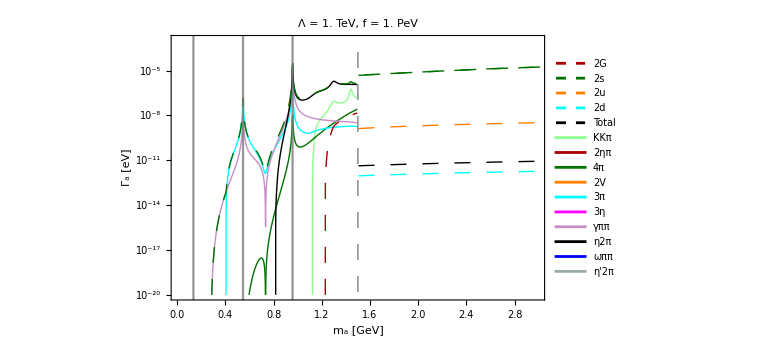

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\Repository\Test\plots\Gluon\decays\Hadronic-widths-Gluon.pdf

```mathematica
hadronicdecayschpt=Join[GroupsClass["Hadronic, ChPT"]];
legending=Join[GroupsClass["Hadronic, ChPT"],{"2G","2s","2u","2d","Total"}]
len=Length[legending];
scale=10^6;
TableRangesMixing=Join[Table[{xx,10^99},{xx,MASS["π^0"]-0.005,MASS["π^0"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η"]-0.005,MASS["η"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η'"]-0.005,MASS["η'"]+0.005,0.001}]];
TableRangesMixing1=Join[Table[{xx,10^-25},{xx,MASS["π^0"]-0.005,MASS["π^0"]+0.005,0.001}],Table[{xx,10^-25},{xx,MASS["η"]-0.005,MASS["η"]+0.005,0.001}],Table[{xx,10^-25},{xx,MASS["η'"]-0.005,MASS["η'"]+0.005,0.001}]];
img=Show[ListLogPlot[Evaluate[Join[Table[{#[[1]],(#[[2]])/scale^2*10^9}&/@Select[GroupWidthTot[group],#[[1]]<maMatch&],{group,hadronicdecayschpt}],Select[{#[[1]],(#[[2]])/scale^2*10^9}&/@SelectedModelWidths[#],#[[1]]>maMatch&]&/@{"2G","2s","2u","2d"},{{#[[1]],(#[[2]])/scale^2*10^9}&/@GroupWidthTot["Hadronic, total"]}]],PlotStyle->{{Thick,Lighter@Lighter@Green},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Orange},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Blue},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Joined->True,Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,2.99},{(10^3./scale)^2 10^-14,(10^3./scale)^2 10^3}},PlotLabel->Style[Row[{"Λ = ",Interpreter["Number"][SelectedModel[[2]]]*10^-3," TeV, f = ",10^-6. scale," PeV"}],18,Black]],
LogLogPlot[{1,1,1,1,1,1,1,1,1,1,1},{x,0.1,1},PlotStyle->{{Thick,Lighter@Lighter@Green},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Orange},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Blue},{Thick,Darker@LightCyan}},PlotLegends->Placed[Style[#,15]&/@Drop[legending,-5],Right]],LogLogPlot[{1,1,1,1,1,1,1,1,1,1,1},{x,0.1,1},PlotStyle->{{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick, Black,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@Drop[legending,len-5],{0.89,0.23}]],ListLogPlot[Evaluate[Table[{maMatch,10^x},{x,-99,99,0.5}]],Joined->True,PlotStyle->{{Thick,Gray,Dashing[0.02]}}],ListLogPlot[Evaluate[TableRangesMixing1], Filling->{1->{Top,Directive[Gray,Opacity[0.2]]},2->{Top,Directive[Gray,Opacity[0.2]]},3->{Top,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",SelectedModel[[1]],"decays",ToString@StringForm["Hadronic-widths-``.pdf",Sequence@@{SelectedModel[[1]]}]}],img]
```

### Total widths

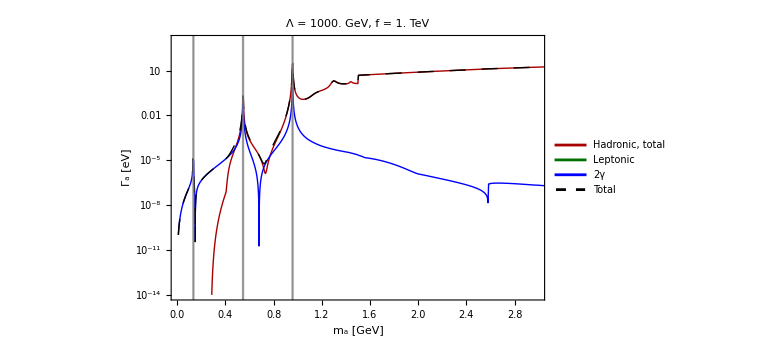

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\Repository\Test\plots\Gluon\decays\Total-widths-Gluon.pdf

```mathematica
decaysplot=Join[GroupsClass["Hadronic, total"],GroupsClass["Non-hadronic"],GroupsClass["Total"]];
scale=1;
img2=Show[ListLogPlot[Evaluate[Table[{#[[1]],#[[2]]*(10^-3*scale)^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthTot[group],#[[1]]>1.75&],GroupWidthTot[group]],{group,decaysplot}]],PlotStyle->{{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@decaysplot,{0.82,0.2}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,2.99},{10^-14,10^3}},PlotLabel->Style[Row[{"Λ = ",SelectedModel[[2]]," GeV, f = ",scale//N," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]},2->{Bottom,Directive[Gray,Opacity[0.2]]},3->{Bottom,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",SelectedModel[[1]],"decays",ToString@StringForm["Total-widths-``.pdf",Sequence@@{SelectedModel[[1]]}]}],img2]
```

### Branching ratios

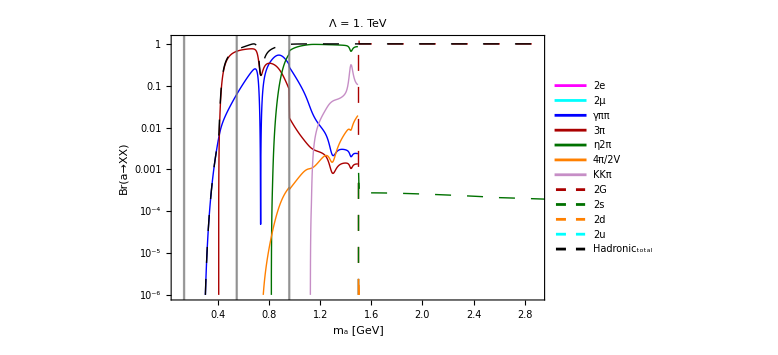

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\Repository\Test\plots\Gluon\decays\Br-ratios-Gluon-scale-1000.-GeV.pdf

```mathematica
brgroup1={"γππ","3π","η2π","4π","KKπ"};
Do[
If[proc=="Hadronic, total",
BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[GroupWidthTot[proc],GroupWidthTot["Total"][[All,{2}]],2];
];
If[proc=="4π",
BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Select[Join[GroupWidthTot[proc][[All,{1}]],{Max[#[[1]],#[[2]]]}&/@Join[GroupWidthTot[proc][[All,{2}]],GroupWidthTot["2V"][[All,{2}]],2],GroupWidthTot["Total"][[All,{2}]],2],#[[1]]<maMatch&];
];
If[!MemberQ[{"Hadronic, total","4π"},proc],
BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Select[Join[GroupWidthTot[proc],GroupWidthTot["Total"][[All,{2}]],2],#[[1]]<maMatch&];
]
,{proc,brgroup1}]
brgroup2={"2e","2μ"};
brlist=Join[brgroup2,brgroup1];
Do[BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[SelectedModelWidths[proc],GroupWidthTot["Total"][[All,{2}]],2],{proc,brgroup2}]
brgroup3={"2G","2s","2d","2u"};
Do[BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[SelectedModelWidths[proc],GroupWidthTot["Total"][[All,{2}]],2],{proc,brgroup3}]
brgroup4={"Hadronic, total"};
Do[BrRatios[proc]={#[[1]],(#[[2]])/(#[[3]])}&/@If[proc=="Hadronic, total",Join[GroupWidthTot[proc],GroupWidthTot["Total"][[All,{2}]],2],Select[Join[GroupWidthTot[proc],GroupWidthTot["Total"][[All,{2}]],2],#[[1]]<maMatch&]],{proc,brgroup4}]
brlist=Join[brgroup2,brgroup1,brgroup3,brgroup4];

BrRatiosPBC["2μ"]={#[[1]],(#[[2]])/(#[[3]])}&/@Join[SelectedModelWidths["2μ"],GroupWidthTot["Leptonic"][[All,{2}]],2];
img3=Show[ListLogPlot[Evaluate[Table[BrRatios[proc],{proc,brlist}]],PlotStyle->{{Thick,Magenta},{Thick,Cyan},{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Orange},{Thick,Lighter@Lighter@Purple},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Br(a→XX)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.09,2.9},{10^-6,1.2}},PlotLabel->Style[Row[{"Λ = ",Interpreter["Number"][SelectedModel[[2]]]*10^-3," TeV"}],18,Black]],LogPlot[{x,x,x,x,x,x,x,x,x,x,x,x,x,x},{x,2,10},PlotStyle->{{Thick,Magenta},{Thick,Cyan},{Thick,Blue},{Thick, Darker@Red},{Thick, Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"2e","2μ","γππ","3π"},{0.45,0.2}]],LogPlot[{x,x,x,x,x,x,x,x,x,x,x,x,x,x},{x,2,10},PlotStyle->{{Thick,Darker@Darker@Green},{Thick,Orange},{Thick,Lighter@Lighter@Purple},{Thick, Darker@Red,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@{"η2π","4π/2V","KKπ","2G"},{0.61,0.2}]],LogPlot[{x,x,x,x,x,x,x,x,x,x,x,x,x,x},{x,2,10},PlotStyle->{{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Black,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@{"2s","2d","2u","Hadronic_total"},{0.86,0.2}]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.2]]},2->{Bottom,Directive[Gray,Opacity[0.2]]},3->{Bottom,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
Export[FileNameJoin[{NotebookDirectory[],"plots",SelectedModel[[1]],"decays",ToString@StringForm["Br-ratios-``-scale-``-GeV.pdf",Sequence@@{SelectedModel[[1]],SelectedModel[[2]]}]}],img3]
```

## Exporting branching ratios (for SensCalc)

```mathematica
ifExportingSensCalc=False;
If[ifExportingSensCalc,
(*Br ratios in terms of the ALP mass*)
gr2=Join[{"2e","2μ","2τ","2γ","π^+π^-π^0","γπ^+π^-","π^+π^-2π^0","2π^+2π^-","η2π^0","ηπ^+π^-","K^(*+)K^(*-)","K^(*0)(K̄)^(*0)","ωπ^+π^-","3π^0","η'2π^0","η'π^+π^-","2ω","2G","2c","2s"},proclistKKπ,{"2ρ^0","ρ^+ρ^-"}];
Do[
mmaxproc=If[MemberQ[{"2e","2μ","2τ","2γ","2G","2c","2s"},proc]==False,maMatch,99999];
mminproc=If[MemberQ[{"2G","2s"},proc]==True,maMatch,0];

BrRatioExport[proc,ma_]=If[mminproc<=ma<mmaxproc,Evaluate[(Interpolation[SelectedModelWidths[proc],InterpolationOrder->1][ma])/(Interpolation[SelectedModelWidths["Total"],InterpolationOrder->1][ma])],0];
,{proc,gr2}];
partlist2Temp=Table[particleslist[proc],{proc,gr2}]/.{{"e","e"}->{"e^+","e^-"},{"μ","μ"}->{"μ^+","μ^-"},{"τ","τ"}->{"τ^+","τ^-"},"A"->"γ","K^0"->"K_L","(K̄)^0"->"K_S",{"G","G"}->{"g","ḡ"},{"D^+","D^+"}->{"c","c̄"},{"K^+","K^+"}->{"s","s̄"}};
partlistFull=Table[Join[partlist2Temp[[i]],Table["Null",4-Length[partlist2Temp[[i]]]]],{i,1,Length[partlist2Temp],1}];
gr2toexp=gr2/.{"2G"->"Jets-GG","2c"->"Jets-cc","2s"->"Jets-ss"};
Listtoexport[ma_]={gr2toexp,partlistFull,Table[BrRatioExport[process,ma],{process,gr2}]};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",SelectedModel[[1]],"decays",ToString@StringForm["Br-ratios-SensCalc-model-``-scale-``-GeV.m",Sequence@@{SelectedModel[[1]],SelectedModel[[2]]}]}],Listtoexport[ma],"MX"]
]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\phenomenology\Gluon\decays\Br-ratios-SensCalc-model-Gluon-scale-1000.-GeV.m

## Comparing two models/scales

## Model importing

```mathematica
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
ModelsListPaths=FileNames["Widths-model-*.m",FileNameJoin[{NotebookDirectory[],"phenomenology"}],Infinity];
ModelsListFilenames=Table[Last@FileNameSplit@ModelsListPaths[[i]],{i,1,Length[ModelsListPaths],1}];
FilenameParameters[i_]:=
StringCases[ModelsListFilenames[[i]],"Widths-model-"~~model__~~"-scale-"~~scale__~~"-GeV.m":>{model,scale}][[1]]
Print["List of available models:"]
ModelsList=Table[FilenameParameters[i],{i,1,Length[ModelsListFilenames],1}]
Print["Selected model:"]
SelectedModels=selectionDialog[ModelsList,"Select two ALP models/scales:"]
SelectedModelsDataTemp=meaningsModels=couplingsValsModels=models=maMatches=SelectedModelsData=SelectedModelsDecays=SelectedModelsDecayGroups=SelectedModelsDecayClasses={0,0};
Do[SelectedModelsDataTemp[[i]]=Import[FileNameJoin[{NotebookDirectory[],"phenomenology",SelectedModels[[i]][[1]],"decays",ToString@StringForm["Widths-model-``-scale-``-GeV.m",Sequence@@{SelectedModels[[i]][[1]],SelectedModels[[i]][[2]]}]}],"MX"];
{models[[i]],couplingsValsModels[[i]],maMatches[[i]]}={SelectedModelsDataTemp[[i]][[1]],SelectedModelsDataTemp[[i]][[2]],SelectedModelsDataTemp[[i]][[3]]};
SelectedModelsData[[i]]=SelectedModelsDataTemp[[i]][[4]]/.{0.->10^-99.,0->10^-99.};
SelectedModelsDecays[[i]]=Drop[SelectedModelsData[[i]][[1]],1];
SelectedModelsDecayGroups[[i]]=Drop[SelectedModelsData[[i]][[2]],1]//DeleteDuplicates;
SelectedModelsDecayClasses[[i]]=Drop[SelectedModelsData[[i]][[3]],1]//DeleteDuplicates;
meaningsModels[[i]]=Take[SelectedModelsData[[i]],{1,3}];
(*Processes belonging to the given group*)
Do[ProcessesGroups[i,group]=(Cases[Transpose[meaningsModels[[i]]],{__,group,__}|{group,__}]//Transpose)[[1]],{group,SelectedModelsDecayGroups[[i]]}];
(*Processes belonging to the given class*)
Do[ProcessesClasses[i,class]=(Cases[Transpose[meaningsModels[[i]]],{__,class}]//Transpose)[[1]],{class,SelectedModelsDecayClasses[[i]]}];
(*Processes groups belonging to the given class*)
Do[GroupsClasses[i,class]=(Cases[Transpose[meaningsModels[[i]]],{__,class}]//Transpose)[[2]]//DeleteDuplicates,{class,SelectedModelsDecayClasses[[i]]}];
Do[SelectedModelsWidths[i,meaningsModels[[i]][[1]][[j]]]=widthProcess[SelectedModelsData[[i]],meaningsModels[[i]][[1]][[j]]],{j,2,Length[meaningsModels[[i]][[1]]],1}];
Do[GroupWidthsTot[i,group]=Join[Drop[SelectedModelsData[[i]],3][[All,{1}]],Sum[SelectedModelsWidths[i,proc][[All,{2}]],{proc,ProcessesGroups[i,group]}],2];
,{group,SelectedModelsDecayGroups[[i]]}]
,{i,1,2,1}];
Print["Coupling patterns:"]
couplingsValsModels//TableForm
Print["Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:"]
maMatches
Print["All decays:"]
SelectedModelsDecays
Print["Decays groups:"]
SelectedModelsDecayGroups
Print["Decays classes:"]
meaningsModels//TableForm
TableRangesMixing=Join[Table[{xx,10^99},{xx,MASS["π^0"]-0.005,MASS["π^0"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η"]-0.005,MASS["η"]+0.005,0.001}],Table[{xx,10^99},{xx,MASS["η'"]-0.005,MASS["η'"]+0.005,0.001}]];
```

List of available models:

(Fermion universal | 1000.
Fermion universal-No-Pheavy | 1000.
Gluon | 1000.
Gluon-kappa-1 | 1000.
Gluon-kappa | 1000.)

Selected model:

(Fermion universal | 1000.
Fermion universal-No-Pheavy | 1000.)

Coupling patterns:

cu
cd
cs
cc
cb
ct
cG
ce
cμ
cτ
cW
cB | 0.873891
0.986109
0.986109
0.873891
1.04676
0.906242
0.
1.05611
1.05611
1.05611
0.
0.
cu
cd
cs
cc
cb
ct
cG
ce
cμ
cτ
cW
cB | 0.873891
0.986109
0.986109
0.873891
1.04676
0.906242
0.
1.05611
1.05611
1.05611
0.
0.

Mass of the ALP (in GeV) at which ChPT and perturbative QCD widths match:

{2.964,1.998}

All decays:

(2e | 2γ | 2μ | 2τ | 2b | 2c | 2d | 2G | 2s | 2t | 2u | 2K_Lπ^0 | 2K_Sπ^0 | 2ηπ^0 | 2π^+2π^- | 2ρ^0 | 2ϕ | 2ω | 3π^0 | 3η | K_LK_Sπ^0 | K^(*0)(K̄)^(*0) | K^-K_Lπ^+ | K^+K_Lπ^- | K^-K_Sπ^+ | K^+K_Sπ^- | K^(*+)K^(*-) | K^+K^-π^0 | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ρ^+ρ^- | ωπ^+π^- | η'2π^0 | η'π^+π^- | Non-hadronic, total | Hadronic, total | Total
2e | 2γ | 2μ | 2τ | 2b | 2c | 2d | 2G | 2s | 2t | 2u | 2K_Lπ^0 | 2K_Sπ^0 | 2ηπ^0 | 2π^+2π^- | 2ρ^0 | 2ϕ | 2ω | 3π^0 | 3η | K_LK_Sπ^0 | K^(*0)(K̄)^(*0) | K^-K_Lπ^+ | K^+K_Lπ^- | K^-K_Sπ^+ | K^+K_Sπ^- | K^(*+)K^(*-) | K^+K^-π^0 | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ρ^+ρ^- | ωπ^+π^- | η'2π^0 | η'π^+π^- | Non-hadronic, total | Hadronic, total | Total)

Decays groups:

(Leptonic | 2γ | QCD jets | KKπ | 2ηπ | 4π | 2V | 3π | 3η | γππ | η2π | ωππ | η'2π | Non-hadronic, total | Hadronic, total | Total
Leptonic | 2γ | QCD jets | KKπ | 2ηπ | 4π | 2V | 3π | 3η | γππ | η2π | ωππ | η'2π | Non-hadronic, total | Hadronic, total | Total)

Decays classes:

m_a, GeV
2e
2γ
2μ
2τ
2b
2c
2d
2G
2s
2t
2u
2K_Lπ^0
2K_Sπ^0
2ηπ^0
2π^+2π^-
2ρ^0
2ϕ
2ω
3π^0
3η
K_LK_Sπ^0
K^(*0)(K̄)^(*0)
K^-K_Lπ^+
K^+K_Lπ^-
K^-K_Sπ^+
K^+K_Sπ^-
K^(*+)K^(*-)
K^+K^-π^0
γπ^+π^-
η2π^0
ηπ^+π^-
π^+π^-2π^0
π^+π^-π^0
ρ^+ρ^-
ωπ^+π^-
η'2π^0
η'π^+π^-
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
Leptonic
2γ
Leptonic
Leptonic
QCD jets
QCD jets
QCD jets
QCD jets
QCD jets
QCD jets
QCD jets
KKπ
KKπ
2ηπ
4π
2V
2V
2V
3π
3η
KKπ
2V
KKπ
KKπ
KKπ
KKπ
2V
KKπ
γππ
η2π
η2π
4π
3π
2V
ωππ
η'2π
η'2π
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
Non-hadronic
Non-hadronic
Non-hadronic
Non-hadronic
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Non-hadronic, total
Hadronic, total
Total
m_a, GeV
2e
2γ
2μ
2τ
2b
2c
2d
2G
2s
2t
2u
2K_Lπ^0
2K_Sπ^0
2ηπ^0
2π^+2π^-
2ρ^0
2ϕ
2ω
3π^0
3η
K_LK_Sπ^0
K^(*0)(K̄)^(*0)
K^-K_Lπ^+
K^+K_Lπ^-
K^-K_Sπ^+
K^+K_Sπ^-
K^(*+)K^(*-)
K^+K^-π^0
γπ^+π^-
η2π^0
ηπ^+π^-
π^+π^-2π^0
π^+π^-π^0
ρ^+ρ^-
ωπ^+π^-
η'2π^0
η'π^+π^-
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
Leptonic
2γ
Leptonic
Leptonic
QCD jets
QCD jets
QCD jets
QCD jets
QCD jets
QCD jets
QCD jets
KKπ
KKπ
2ηπ
4π
2V
2V
2V
3π
3η
KKπ
2V
KKπ
KKπ
KKπ
KKπ
2V
KKπ
γππ
η2π
η2π
4π
3π
2V
ωππ
η'2π
η'2π
Non-hadronic, total
Hadronic, total
Total | m_a, GeV
Non-hadronic
Non-hadronic
Non-hadronic
Non-hadronic
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, perturbative
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Hadronic, ChPT
Non-hadronic, total
Hadronic, total
Total

## Plots

### Hadronic vs leptonic vs photonic widths

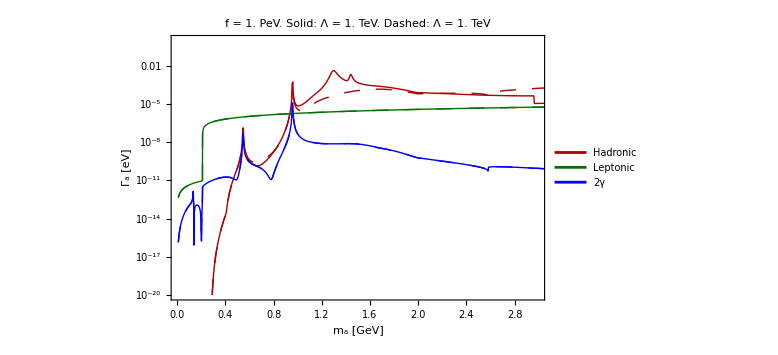

```mathematica
Do[decaysplots[i]=Join[GroupsClasses[i,"Hadronic, total"],GroupsClasses[i,"Non-hadronic"],GroupsClasses[i,"Total"]],{i,1,2,1}];
fval=10^6;
img2=Show[ListLogPlot[Evaluate[Join[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[1,group],#[[1]]>1.75&],GroupWidthsTot[1,group]],{group,Select[decaysplots[1],#!="Total"&]}],Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[2,group],#[[1]]>1.75&],GroupWidthsTot[2,group]],{group,Select[decaysplots[2],#!="Total"&]}]]],PlotStyle->{{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@{"Hadronic","Leptonic","2γ"},{0.85,0.2}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.01,2.99},{(10^3/fval)^2 10^-14,(10^3/fval)^2 10^6}},PlotLabel->Style[Row[{"f = ", fval*10^-6., " PeV. Solid: Λ = ",Interpreter["Number"][ModelsList[[1]][[2]]] 10^-3.," TeV. Dashed: Λ = ",Interpreter["Number"][ModelsList[[2]][[2]]] 10^-3.," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Top,Directive[Gray,Opacity[0.2]]},2->{Top,Directive[Gray,Opacity[0.2]]},3->{Top,Directive[Gray,Opacity[0.2]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
(*Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Total-widths-``.pdf",Sequence@@{SelectedModels[[1]][[1]]}]}],img2]*)
```

### Plot 2

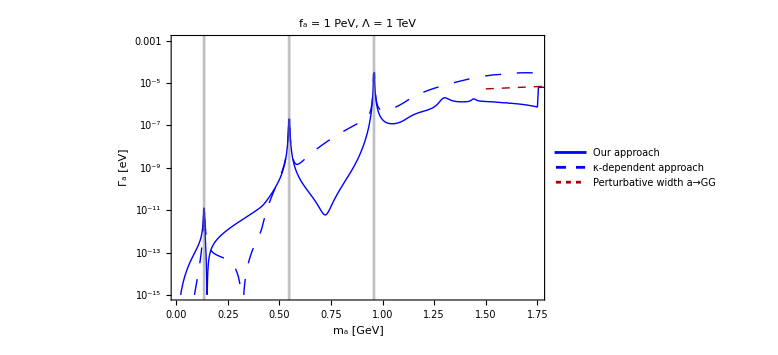

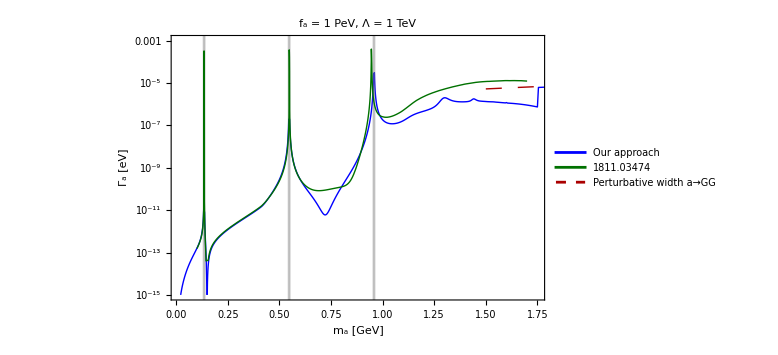

```mathematica
αsData[q_] = Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/AlphaS.txt"}],"Table"]][q];
ΓGGwidthTemp[ma_,fa_]=(αsData[ma]^2 (83 αsData[ma]+4 π) cG^2 ma^3)/(32 π^4 fa^2)/.{cG->1};
GGwidthData=Table[{ma,10^9 ΓGGwidthTemp[ma,10^6.]},{ma,1.5,2,0.01}];
Do[
decaysplots[i]=Join[GroupsClasses[i,"Hadronic, total"],GroupsClasses[i,"Non-hadronic"],GroupsClasses[i,"Total"]]
,{i,1,2,1}];
fval=10^6;
Γaloni=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/temp/WidthsAloni.m"}],"MX"];
ΓaloniTotal[ma_]=1/(((*32*Pi*)16 Pi^2)^2)(10^3/fval)^2 Select[Γaloni,#[[1]]=="Total"&][[1]][[2]];
img2=Show[ListLogPlot[Evaluate[Join[Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[1,group],#[[1]]>1.75&],GroupWidthsTot[1,group]],{group,{"Total"}}],1],Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[2,group],#[[1]]>1.75&],GroupWidthsTot[2,group]],{group,{"Total"}}],1],{GGwidthData}]],PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"Our approach","κ-dependent approach","Perturbative width a→GG"},{0.7,0.16}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->{{0.01,1.75},{(10^3/fval)^2 10^-9,(10^3/fval)^2 10^3}},PlotLabel->Style[Row[{"f_a = ", IntegerPart[fval*10^-6.], " PeV, Λ = ",1," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.1]]},2->{Top,Directive[Gray,Opacity[0.1]]},3->{Top,Directive[Gray,Opacity[0.1]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
img2=Show[ListLogPlot[Evaluate[Join[Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[1,group],#[[1]]>1.75&],GroupWidthsTot[1,group]],{group,{"Total"}}],1],{Table[{m,1000},{m,0.1,3,0.1}]},{GGwidthData}]],PlotStyle->{{Thick,Blue},{Thick,Darker@Darker@Green},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"Our approach","1811.03474","Perturbative width a→GG"},{0.7,0.16}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->{{0.01,1.75},{(10^3/fval)^2 10^-9,(10^3/fval)^2 10^3}},PlotLabel->Style[Row[{"f_a = ", IntegerPart[fval*10^-6.], " PeV, Λ = ",1," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.1]]},2->{Top,Directive[Gray,Opacity[0.1]]},3->{Top,Directive[Gray,Opacity[0.1]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}],LogPlot[ΓaloniTotal[ma],{ma,0.1,1.7},PlotRange->All,PlotStyle->{{Thick,Darker@Darker@Green}}]]
(*Export[FileNameJoin[{NotebookDirectory[],"plots",ToString@StringForm["Total-widths-``.pdf",Sequence@@{SelectedModels[[1]][[1]]}]}],img2]*)
```

### Gluonic ALPs - comparison of the results of this work with Aloni+

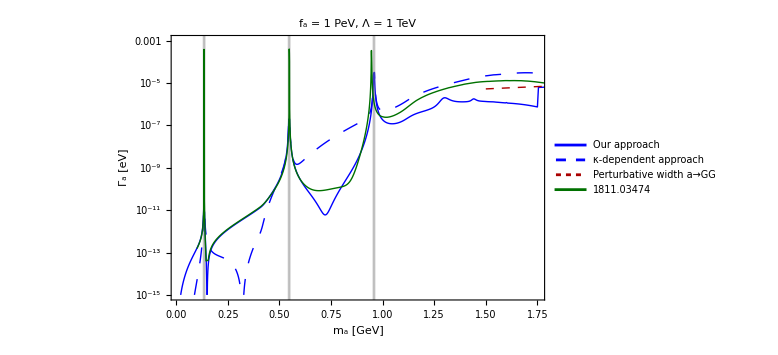

```mathematica
img2=Show[ListLogPlot[Evaluate[Join[Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[1,group],#[[1]]>1.75&],GroupWidthsTot[1,group]],{group,{"Total"}}],1],Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[2,group],#[[1]]>1.75&],GroupWidthsTot[2,group]],{group,{"Total"}}],1],{GGwidthData},{Table[{m,1000},{m,0.1,3,0.1}]}]],PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.01]},{Thick,Darker@Darker@Green},{Thick,Blue,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"Our approach","κ-dependent approach","Perturbative width a→GG","1811.03474"},{0.7,0.16}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->{{0.01,1.75},{(10^3/fval)^2 10^-9,(10^3/fval)^2 10^3}},PlotLabel->Style[Row[{"f_a = ", IntegerPart[fval*10^-6.], " PeV, Λ = ",1," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.1]]},2->{Top,Directive[Gray,Opacity[0.1]]},3->{Top,Directive[Gray,Opacity[0.1]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}],LogPlot[ΓaloniTotal[ma],{ma,0.1,1.85},PlotRange->All,PlotStyle->{{Thick,Darker@Darker@Green}}]]
```

### Plot - widths fermionic vs gluonic

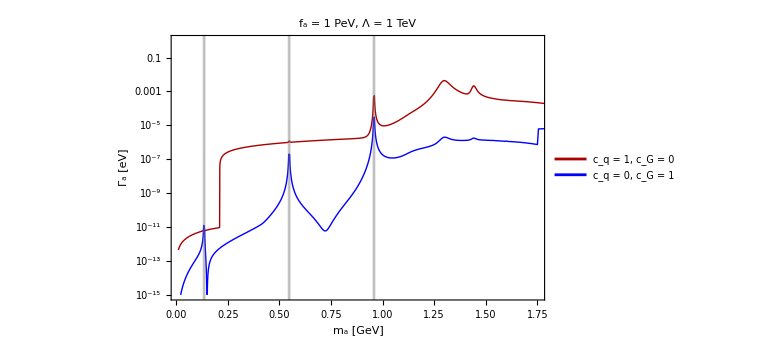

```mathematica
Show[ListLogPlot[Evaluate[Join[Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[1,group],#[[1]]>1.75&],GroupWidthsTot[1,group]],{group,{"Total"}}],1],Take[Table[{#[[1]],(#[[2]])/fval^2*10^9}&/@If[group=="QCD jets",Select[GroupWidthsTot[2,group],#[[1]]>1.75&],GroupWidthsTot[2,group]],{group,{"Total"}}],1]]],PlotStyle->{{Thick,Darker@Red},{Thick,Blue},{Thick,Darker@Red,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"c_q = 1, c_G = 0","c_q = 0, c_G = 1"},{0.7,0.16}],Joined->True,PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "Γ_a [eV]"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->{{0.01,1.75},{(10^3/fval)^2 10^-9,(10^3/fval)^2 10^6}},PlotLabel->Style[Row[{"f_a = ", IntegerPart[fval*10^-6.], " PeV, Λ = ",1," TeV"}],18,Black]],ListLogPlot[Evaluate[TableRangesMixing], Filling->{1->{Bottom,Directive[Gray,Opacity[0.1]]},2->{Top,Directive[Gray,Opacity[0.1]]},3->{Top,Directive[Gray,Opacity[0.1]]},4->{True,Directive[Blue,Opacity[0.05]]},5->{True,Directive[Darker@Darker@Green,Opacity[0.05]]},6->{True,Directive[Darker@Red,Opacity[0.05]]}}]]
```

# ALP production

## Launching routines

```mathematica
listFacility={"FermilabBD","LHC","SPS"};
Print["Calculating the branching ratios of the ALP production in B meson decays..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"production","B-decays.nb"}]];
];//AbsoluteTiming
Print["Calculating the branching ratios of the ALP production via proton bremsstrahlung (may take a while)..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"production","proton-bremsstrahlung.nb"}]];
];//AbsoluteTiming
Print["Calculating the branching ratios of the ALP production in decays of different mesons..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"production","mesons-decays.nb"}]];
];//AbsoluteTiming
Print["Calculating the branching ratios of the ALP production via fragmentation..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"production","fragmentation.nb"}]];
];//AbsoluteTiming
  Print["Calculating the probabilities of the ALP production in the Drell-Yan process..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"production","drell-yan.nb"}]];
];//AbsoluteTiming
```

Calculating the branching ratios of the ALP production in B meson decays...

{1.13617,Null}

Calculating the branching ratios of the ALP production via proton bremsstrahlung (may take a while)...

{53.7009,Null}

Calculating the branching ratios of the ALP production in decays of different mesons...

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson p1 is not on-shell. Please put it on-shell via ScalarProduct[p1,p1]=0

{56.9396,Null}

Calculating the branching ratios of the ALP production via fragmentation...

{3.70486,Null}

Calculating the probabilities of the ALP production in the Drell-Yan process...

{0.669087,Null}

## Making comparison plot and producing tabulated output

```mathematica
Print["Model:"]
modelChoice=ModelSelector
{Λchoice,facilityChoice}=DialogInput[Module[{ΛChoice=1000.0,facilityChoice="SPS"},Column[{(*1) Let the user open the specialized model selector*)TextCell["Enter the scale Λ in GeV (>top mass):"],InputField[Dynamic[ΛChoice],Number],Spacer[10],(*3) Facility selection*)TextCell["Pick a facility:"],RadioButtonBar[Dynamic[facilityChoice],listFacility],Spacer[10],(*Final buttons to exit or cancel*)Row[{Button["OK",DialogReturn[{ΛChoice,facilityChoice}],Enabled->Dynamic[facilityChoice=!=None],ImageSize->{80,30}],Spacer[20],Button["Cancel",DialogReturn[None],ImageSize->{80,30}]}]}]]]
Print["Production channels:"]
YieldsFromLightMesons[modelChoice,Λchoice];
ProductionChannels=Keys[DownValues@PALPprod][[All,1,1]]//DeleteDuplicates;
(*Temporary assignment - remove mixing production*)
ProductionChannels=Select[ProductionChannels,!StringContainsQ[#,"Mixing"]&]
```

Model:

Fermion universal

{1000.,SPS}

Production channels:

{B,Bremsstrahlung,Fragmentation,Drell-Yan,K_S,ρ^+,η,η',ω}

## Plot

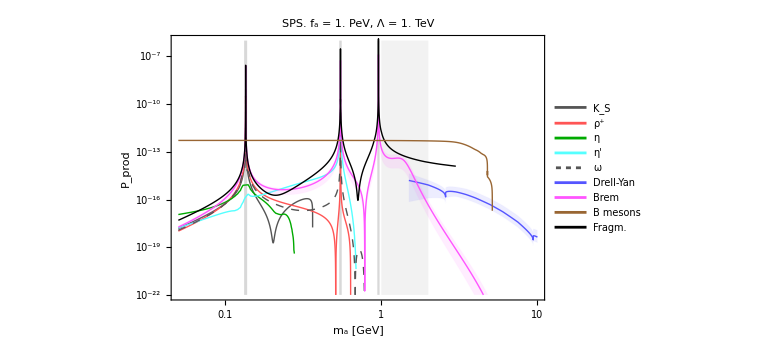

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\plots\Fermion universal\production\production-total-Fermion universal-SPS.pdf

```mathematica
fval=10^6.;
ptrange={{0.05,10},{10^-22,10^-6}};
PlotFrame=LogLogPlot[Evaluate[{10^30 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^30 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^10 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)],10^10 UnitStep[ma-1.]*UnitStep[2-ma]}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[0.02]},{Thick, Darker@Red},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Green},{Thick,Darker@Green,Dashing[0.02]},{Thick,Black},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"m_a [GeV]" , "P_prod"},FrameStyle->Directive[Black, 23,Thick],ImageSize->Large,PlotRange->ptrange,PlotLabel->Style[Row[{facilityChoice, ". f_a = ", 10^-6. fval," PeV, Λ = ",10^-3. Λchoice," TeV"}],22,Black],Filling->{1->{Bottom,Directive[Gray,Opacity[0.3]]},2->{Bottom,Directive[Gray,Opacity[0.3]]},3->{Bottom,Directive[Gray,Opacity[0.3]]},4->{Bottom,Directive[Gray,Opacity[0.1]]}}];
PlotLightMesons=LogLogPlot[Evaluate[Table[PALPprod[prod,modelChoice,facilityChoice,ma,fval,Λchoice],{prod,listLightMesons}]],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Lighter@Black},{Thick, Lighter@Red},{Thick,Darker@Green},{Thick,Lighter@Cyan},{Thick,Lighter@Black,Dashing[0.01]}},Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}}];
PlotDrellYan=LogLogPlot[Evaluate[{PALPprod["Drell-Yan",modelChoice,facilityChoice,ma,fval,Λchoice],PALPprodLower["Drell-Yan",modelChoice,facilityChoice,ma,fval,Λchoice],PALPprodUpper["Drell-Yan",modelChoice,facilityChoice,ma,fval,Λchoice]}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Lighter@Blue},{Thick,Directive[Lighter@Blue,Opacity[0.01]]},{Thick,Directive[Lighter@Blue,Opacity[0.01]]}},Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}},Filling->{2->{{3},Directive[Lighter@Blue,Opacity[0.1]]}}];
PlotBrem=LogLogPlot[Evaluate[{PALPprod["Bremsstrahlung",modelChoice,facilityChoice,ma,fval,Λchoice],PALPprodLower["Bremsstrahlung",modelChoice,facilityChoice,ma,fval,Λchoice],PALPprodUpper["Bremsstrahlung",modelChoice,facilityChoice,ma,fval,Λchoice]}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Lighter@Magenta},{Thick,Directive[Lighter@Magenta,Opacity[0.01]]},{Thick,Directive[Lighter@Magenta,Opacity[0.01]]}},Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}},Filling->{2->{{3},Directive[Lighter@Magenta,Opacity[0.1]]}}];
PlotBmesons=LogLogPlot[Evaluate[{PALPprod["B",modelChoice,facilityChoice,ma,fval,Λchoice]}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Brown}},Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}}];
PlotFragmentation=LogLogPlot[Evaluate[{PALPprod["Fragmentation",modelChoice,facilityChoice,ma,fval,Λchoice]}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Black},{Thick,Directive[Lighter@Magenta,Opacity[0.01]]},{Thick,Directive[Lighter@Magenta,Opacity[0.01]]}},Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}},Filling->{2->{{3},Directive[Lighter@Magenta,Opacity[0.1]]}}];
PlotWithLegends1=LogLogPlot[Evaluate[{10^99,10^99,10^99,10^99,10^99,10^99,10^99,10^99,10^99}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Lighter@Black},{Thick, Lighter@Red},{Thick,Darker@Green},{Thick,Lighter@Cyan},{Thick,Lighter@Blue},{Thick,Lighter@Magenta},{Thick,Brown}},PlotLegends->Placed[Style[#,18]&/@Join[Drop[listLightMesons,-1]],{0.64,0.76}],Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}},Filling->{2->{{3},Directive[Lighter@Magenta,Opacity[0.1]]}}];
PlotWithLegends2=LogLogPlot[Evaluate[{10^99,10^99,10^99,10^99,10^99,10^99,10^99,10^99,10^99}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Lighter@Black,Dashing[0.01]},{Thick,Lighter@Blue},{Thick,Lighter@Magenta},{Thick,Brown},{Thick,Black}},PlotLegends->Placed[Style[#,18]&/@Join[Take[listLightMesons,-1],{"Drell-Yan","Brem","B mesons","Fragm."}],{0.84,0.76}],Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}},Filling->{2->{{3},Directive[Lighter@Magenta,Opacity[0.1]]}}];
(*PlotMixing=LogLogPlot[Evaluate[{PALPprod["Mixing-π^0",modelChoice,"SPS",ma,fval,Λchoice]+PALPprod["Mixing-η",modelChoice,facilityChoice,ma,fval,Λchoice]+PALPprod["Mixing-η'",modelChoice,facilityChoice,ma,fval,Λchoice]}],{ma,0.05,10},PlotPoints->500,PlotStyle->{{Thick,Brown}},Frame-> True,ImageSize->Large,PlotRange->{{0.05,10},{10^-22,100}},Filling->{2->{{3},Directive[Lighter@Magenta,Opacity[0.1]]}}];*)
PlotTotalProduction=Show[PlotFrame,PlotLightMesons,PlotDrellYan,PlotBrem,PlotFragmentation,PlotBmesons,PlotWithLegends1,PlotWithLegends2]
Export[FileNameJoin[{NotebookDirectory[],"plots",modelChoice,"production","production-total-"<>modelChoice<>"-"<>facilityChoice<>".pdf"}],PlotTotalProduction]
```

### Exclusive channels vs old “production via mixing”

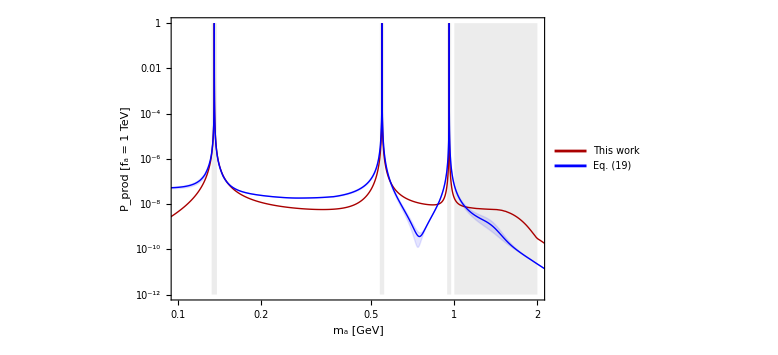

```mathematica
Λchoice=10^3.;
unc={"Central","Lower","Upper"};
prodlists=Join[{"Fragmentation"},listLightMesons,{"Bremsstrahlung"}];
Do[
PALPprodLight[model,unct,"FermilabBD",ma_,10^3.,Λchoice]=Sum[If[prod=="Bremsstrahlung"&&unct!="Central",Symbol["PALPprod"<>unct],PALPprod][prod,model,"FermilabBD",ma,10^3.,Λchoice],{prod,prodlists}]
,{unct,unc},{model,ModelListAll}]
LogLogPlot[Evaluate[{PALPprod["Old-Mixing","Gluon","FermilabBD",ma,10^3.,Λchoice],PALPprodLight["Gluon","Central","FermilabBD",ma,10^3.,Λchoice],PALPprodLight["Gluon","Lower","FermilabBD",ma,10^3.,Λchoice],PALPprodLight["Gluon","Upper","FermilabBD",ma,10^3.,Λchoice],10^3 UnitStep[(MASS["π^0"]+0.003)-ma]*UnitStep[ma-(MASS["π^0"]-0.003)],10^3 UnitStep[(MASS["η"]+0.01)-ma]*UnitStep[ma-(MASS["η"]-0.01)],10^3 UnitStep[(MASS["η'"]+0.016)-ma]*UnitStep[ma-(MASS["η'"]-0.016)],10^3 UnitStep[ma-1.]*UnitStep[2-ma]}],{ma,0.05,3},ImageSize->Large,Frame->True,PlotPoints->1000,FrameStyle->Directive[Thick,Black,22],FrameLabel->{"m_a [GeV]","P_prod [f_a = 1 TeV]"},PlotStyle->{{Thick,Darker@Red},{Thick,Blue},{Thick,Blue,Opacity[0.1]},{Thick,Blue,Opacity[0.1]},{Thick,Gray},{Thick,Gray},{Thick,Gray},{Thick,Gray}},PlotRange->{{0.1,2},{10^-12,1}},Filling->{3->{{4},Directive[Blue,Opacity[0.1]]},5->{Bottom,Directive[Gray,Opacity[0.15]]},6->{Bottom,Directive[Gray,Opacity[0.15]]},7->{Bottom,Directive[Gray,Opacity[0.15]]},8->{Bottom,Directive[Gray,Opacity[0.15]]}},PlotLegends->Placed[Style[Row[{#}],18,Black]&/@{"This work","Eq. (19)"},{0.2,0.2}]]
```

## Exporting tabulated production probabilities

```mathematica
malist=Select[Table[ma,{ma,0.05,10.,0.005}],!MemberQ[MASS[#]&/@{"π^0","η","η'"},#]&];
prodProbListTemp[ma_]=Join[{ma},PALPprod[#,modelChoice,facilityChoice,ma,1.,Λchoice]&/@ProductionChannels];
ProductionChannelsCSV=("Pprod "<>#)&/@(ProductionChannels/.{"K_S"->"Ks","ρ^+"->"RhoCharged","η"->"Eta","η'"->"EtaPr","ω"->"Omega","Mixing-π^0"->"Mixing-Pi0","Mixing-η"->"Mixing-Eta","Mixing-η'"->"Mixing-EtaPr"});
ExplanationList=Join[{"ma [GeV]"},ProductionChannelsCSV];
tabProbabilitiesToExport[facilityChoice]=Table[prodProbListTemp[ma],{ma,malist}];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modelChoice,"production","ProductionProbabilities-Lambda-"<>(N[10^-3 Λchoice]//CForm//ToString)<>"-TeV.csv"}],Join[{ExplanationList},tabProbabilitiesToExport[facilityChoice]],"CSV"]
```

InterpolatingFunction::dmval: Input value {1.61044} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.61144} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.61243} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\phenomenology\Gluon\production\ProductionProbabilities-Lambda-1.-TeV.csv

### Exporting branching ratios of separate decays

```mathematica
prodred=Select[ProductionChannels,!MemberQ[{"Mixing","Drell-Yan","Bremsstrahlung","Fragmentation"},#]&]
{#,listProcessesMeson[#]}&/@prodred;
replacementRuleMesonDecay["B","B"]="B";
combinations=Flatten[Table[Table[{meson,listProcessesMeson[meson][[i]]},{i,1,Length[listProcessesMeson[meson]],1}],{meson,prodred}],1]
(*Standard tabulated format*)
prodProbListTemp[ma_]=Join[{ma},Table[With[{mes=combinations[[i]][[1]],proc=combinations[[i]][[2]]},If[mes!="B",Re[BrLightMesons[ma,Fπ,mes,proc,modelChoice,Λchoice]],BrBtoALP["Total",modelChoice,ΛChoice,ma,Fπ]]],{i,1,Length[combinations],1}]];
malist=Select[Table[ma,{ma,0.05,10.,0.005}],!MemberQ[MASS[#]&/@{"π^0","η","η'"},#]&];
ProductionChannelsCSV=("Br_"<>replacementRuleMesonDecay[#[[1]],#[[2]]])&/@combinations;
ExplanationList=Join[{"ma [GeV]"},ProductionChannelsCSV];
tabProbabilitiesToExport[facilityChoice]=Table[prodProbListTemp[ma],{ma,malist}];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modelChoice,"production","BrRatios-"<>modelChoice<>"-Lambda-"<>(N[10^-3 Λchoice]//CForm//ToString)<>"-TeV.csv"}],Join[{ExplanationList},tabProbabilitiesToExport[facilityChoice]],"CSV"]
```

{B,K_S,ρ^+,η,η',ω}

(B | B
K_S | aπ^0
ρ^+ | πa
η | a2π^0
η | aπ^+π^-
η' | a2π^0
η' | aπ^+π^-
ω | aγ
ω | aπ^+π^-)

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\phenomenology\Gluon\production\BrRatios-Gluon-Lambda-1.-TeV.csv

### Exporting for SensCalc

#### Branching ratios

```mathematica
TableForExportSensCalc[ma_,E1_,E3_]=Table[With[{mes=combinations[[i]][[1]],proc=combinations[[i]][[2]],procrepl=replacementRuleMesonDecay[combinations[[i]][[1]],combinations[[i]][[2]]]},{procrepl,If[mes!="B",Re[BrLightMesons[ma,Fπ,mes,proc,modelChoice,Λchoice]],BrBtoALP["Total",modelChoice,ΛChoice,ma,Fπ]],If[MemberQ[procs3body,combinations[[i]]],M2numeric[modelChoice,procrepl,ma,ΛChoice,E1,E3],0.]}],{i,1,Length[combinations],1}];
TableForExportSensCalc[ma_,E1_,E3_]=Join[TableForExportSensCalc[ma,E1,E3],{{"Bplus-to-Kplus",BrBtoALP["K^+",modelChoice,ΛChoice,ma,Fπ],0.},{"B0-to-Kstar",BrBtoALP["K^*(892)",modelChoice,ΛChoice,ma,Fπ],0.}}];
modelrepl=If[modelChoice=="Fermion universal","ALP-fermion",If[modelChoice=="Gluon","ALP-gluon",modelChoice]]
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modelChoice,"For SensCalc","BrRatios-Msquared-LightMesonDecays-"<>modelrepl<>"-Lambda="<>(N[10^-3 Λchoice]//CForm//ToString)<>"-TeV.mx"}],TableForExportSensCalc[mLLP,E1,E3],"MX"]
```

ALP-gluon

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\phenomenology\Gluon\For SensCalc\BrRatios-Msquared-LightMesonDecays-ALP-gluon-Lambda=1.-TeV.mx

#### Coefficients and couplings

```mathematica
tabcoeffsExport[mLLP_]={{"[(σ_DIS/σ_DIS) |c_(G, eff)|^2]_(ϵ = 1)",Abs[cGval[mLLP,modelChoice,ΛChoice]/Fπ]^2},{"|θ_(π^0)|^2 (ϵ = 1)",θ2m0a[modelChoice,ΛChoice,"π^0",mLLP,Fπ]},{"|θ_ηa|^2 (ϵ = 1)",θ2m0a[modelChoice,ΛChoice,"η",mLLP,Fπ]},{"|θ_(η' a)|^2 (ϵ = 1)",θ2m0a[modelChoice,ΛChoice,"η'",mLLP,Fπ]},{"g_app (ϵ = 1)",gaNNnumeric[mLLP,cRGval[modelChoice,ΛChoice,"cu"],cRGval[modelChoice,ΛChoice,"cd"],cRGval[modelChoice,ΛChoice,"cs"],cRGval[modelChoice,ΛChoice,"cG"],Fπ]}};
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modelChoice,"For SensCalc","Coefficients-"<>modelrepl<>"-Lambda="<>(N[10^-3 Λchoice]//CForm//ToString)<>"-TeV.mx"}],tabcoeffsExport[mLLP],"MX"]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\phenomenology\Gluon\For SensCalc\Coefficients-ALP-gluon-Lambda=1.-TeV.mx

### Exporting tabulated angle-energy distributions (currently - fragmentation process only)

```mathematica
Do[
DoubleDistrFragmentationSelected[mass,θLLP_,ELLP_]=DoubleDistrALPfragmentation[modelChoice,facilityChoice,mass,Λchoice,θLLP,ELLP];
DoubleDistrFragmentationTabulated[mass]=Flatten[Table[{mass,θLLP,ELLP,DoubleDistrFragmentationSelected[mass,θLLP,ELLP]},{θLLP,θNlist[facilityChoice]},{ELLP,ENlist[facilityChoice]}],1]//Developer`ToPackedArray;
,{mass,MassListFragm}];
DoubleDistrTabulated=(Join[##]&@@(DoubleDistrFragmentationTabulated[#]&/@MassListFragm))//N//Developer`ToPackedArray;
modname=If[modelChoice=="Gluon","ALP-gluon",If[modelChoice=="Fermion universal","ALP-fermion",modelChoice]];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modelChoice,"spectra","DoubleDistr_"<>modname<>"_Fragmentation_"<>facilityChoice<>".m"}],DoubleDistrTabulated,"MX"]
```

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\phenomenology\Gluon\spectra\DoubleDistr_ALP-gluon_Fragmentation_SPS.m

```mathematica
(*
modelsfacilities=Flatten[Table[{model,facility},{model,{"Fermion universal","Gluon"}},{facility,FacListFragm}],1]
ResourceFunction["MonitorProgress"]@Do[
Module[{facilityChoice=facmod[[2]],modelChoice=facmod[[1]],Λchoice=10^3.},
If[MemberQ[FacListFragm,facilityChoice],
ResourceFunction["MonitorProgress"]@Do[
DoubleDistrFragmentationSelected[mass,θLLP_,ELLP_]=DoubleDistrALPfragmentation[modelChoice,facilityChoice,mass,Λchoice,θLLP,ELLP];
DoubleDistrFragmentationTabulated[mass]=Flatten[Table[{mass,θLLP,ELLP,DoubleDistrFragmentationSelected[mass,θLLP,ELLP]},{θLLP,θNlist[facilityChoice]},{ELLP,ENlist[facilityChoice]}],1]//Developer`ToPackedArray;
,{mass,MassListFragm}];
DoubleDistrTabulated=(Join[##]&@@(DoubleDistrFragmentationTabulated[#]&/@MassListFragm))//N//Developer`ToPackedArray;
modname=If[modelChoice=="Gluon","ALP-gluon",If[modelChoice=="Fermion universal","ALP-fermion",modelChoice]];
Export[FileNameJoin[{NotebookDirectory[],"phenomenology",modelChoice,"spectra","DoubleDistr_"<>modname<>"_Fragmentation_"<>facilityChoice<>".m"}],DoubleDistrTabulated,"MX"]
]
]
,{facmod,modelsfacilities}]
*)
```

```mathematica
tabCouplings[ma_,fa_]=gaNNnumeric[ma,cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cG"],fa]&/@{"Fermion universal","Gluon"};
(*Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"auxiliary data/appCouplings.mx"}],{{"ALP-fermion","ALP-gluon"},tabCouplings[ma,Fπ/ϵ]}//Transpose,"MX"];*)
```

# Deleting generated cells

```mathematica
Deleting generated cells
FrontEndTokenExecute["DeleteGeneratedCells"];
FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];
```

{16.2928,Null}

Defining Feynman rules for various vertices...

{0.83909,Null}